```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles

{Answers,BulkStats,.DS_Store,MoviesByPeople,MoviesByPeopleMinusProbe,PeopleByMovies,PeopleByMoviesMinusProbe,ProbeStuff,sortedscores,ssq,ssqeval,synqual,synqual2}

### Titles

```mathematica
(*titles=Import["movie_titles.txt","CSV"];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
titles>>titles;
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize"]*)
```

Some of the titles have 3 columns, some have 4-6, as commas in the title create separate columns in CSV.  Columns 1 and 2 remain constant in interpretation throughout--movie # and year.

### Probe

```mathematica
(*probe=Import["probe.txt","Table"];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
probe>>probe;
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize"]*)
```

Parse into different movies

```mathematica
namesmma=Table[0,{17770}];
Do[{pl=PadLeft[IntegerDigits[i],7],
rh=StringJoin[Table[ToString[pl[[i]]],{i,7}]],
lh="movie",
namesmma[[i]]=StringJoin[lh,rh]
},{i,17770}]
```

```mathematica
pointer=0;
mm=Table[{},{20000}];
Do[If[StringQ[probe[[i,1]]]==True, {pointer+=1,mm[[pointer]]=probe[[i]]},AppendTo[mm[[pointer]],probe[[i,1]]]],{i,1,Length[probe]}];
mm2=DeleteCases[mm,{}];
Length[mm2]
```

16938

```mathematica
probe[[2]]
```

{10:,1952305,1531863}

#### Functions I'll need for parsing

```mathematica
nameparser[movienumberstring_]:=
{
a=StringPosition[movienumberstring,":"][[1,1]];
b=StringTake[movienumberstring,{1,a-1}];
c=ToExpression[b]
}[[1]]
```

```mathematica
numbertoname[n_]:=
{
pl=PadLeft[IntegerDigits[n],7];
rh=StringJoin[Table[ToString[pl[[i]]],{i,7}]];
lh="movie";
StringJoin[lh,rh]
}[[1]]
```

```mathematica
probescores=Table[0,{Length[probe]}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TrainingMma"];
Do[
{
nmp=nameparser[probe[[i,1]]];
a=Get[numbertoname[nmp]];
probescores[[i]]=Table[Join[{nmp},a[[Position[a,probe[[i,j]]][[1,1]]]]],{j,2,Length[probe[[i]]]}];
Clear[a];
If[IntegerQ[i/100]==True,Print[i]]
},{i,Length[probe]}
]
```

```mathematica
probescores>>probescores;
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles

```mathematica
FileNames[]
```

{BulkStats,.DS_Store,PeopleByMovies,peopleids,probe,synqual,TestFolder,titles,TrainingMma}

### Put together the qualifying list

```mathematica
(*qualifying=Import["qualifying.txt","CSV"];
Dimensions[qualifying]*)
```

First parse into different movies

```mathematica
(*pointer=0;
mm=Table[{},{20000}];
Do[If[Length[qualifying[[i]]]==1, pointer+=1,AppendTo[mm[[pointer]],qualifying[[i]]]],{i,Length[qualifying]}]
mm2=DeleteCases[mm,{}];
Length[mm2]*)
```

Then parse out the different movie names

```mathematica
(*pointer=0;
movienums=Table[0,{20000}];
Do[If[Length[qualifying[[i]]]==1,{ pointer+=1,movienums[[pointer]]=qualifying[[i]]}],{i,Length[qualifying]}]
movienums=DeleteCases[movienums,0];
Length[movienums]*)
```

```mathematica
(*syndata=mm2;
Do[syndata[[i,j]]=Prepend[mm2[[i,j]],movienums[[i]][[1]]],{i,Length[mm2]},{j,Length[mm2[[i]]]}];*)
```

### Transforming dates

```mathematica
getdash[string_]:=StringPosition[string,"-"]
getdate[datestring_]:=
{
a=getdash[datestring];
year=ToExpression[StringTake[datestring,{1,a[[1,1]]-1}]];
month=ToExpression[StringTake[datestring,{a[[1,1]]+1,a[[2,1]]-1}]];
day=ToExpression[StringTake[datestring,{a[[2,1]]+1,StringLength[datestring]}]];
{year,month,day}
}[[1]]
```

```mathematica
<<Calendar`
```

```mathematica
(*datecoord[i_]:=DaysBetween[{1997,1,1},getdate[fsyn[[i,3]]]]
 datetable=Table[datecoord[i],{i,Length[fsyn]}];//Timing
Dimensions[qualifying][[1]]-Length[fsyn]*)
```

```mathematica
(*fsyn=Flatten[syndata,1];syntable=Table[{fsyn[[i,1]],fsyn[[i,2]],datetable[[i]]},{i,Length[datetable]}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
syntable>>synqual;
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize"]*)
```

### Assemble the training files

Make names for everything in the training set

```mathematica
names=Table[0,{17770}];
Do[{pl=PadLeft[IntegerDigits[i],7],
rh=StringJoin[Table[ToString[pl[[i]]],{i,7}]],
lh="mv_",
suffix=".txt",
names[[i]]=StringJoin[lh,rh,suffix]
},{i,17770}]
```

```mathematica
namesmma=Table[0,{17770}];
Do[{pl=PadLeft[IntegerDigits[i],7],
rh=StringJoin[Table[ToString[pl[[i]]],{i,7}]],
lh="movie",
namesmma[[i]]=StringJoin[lh,rh]
},{i,17770}]
```

Transform all of the training files into Mathematica files and put them in a safe place

```mathematica
<<Calendar`
```

```mathematica
datecoordtest[i_] := DaysBetween[{1997, 1, 1}, getdate[test[[i, 3]]]];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/training_set"];
```

```mathematica
Do[
{test=Import[names[[i]],"CSV"],
test=Delete[test,1],
test=Table[{ToExpression[test[[i,1]]],ToExpression[test[[i,2]]],datecoordtest[i]},{i,Length[test]}],
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/TestFiles"],
Print[namesmma[[i]]],
Put[test,namesmma[[i]]],
Clear[test],
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/training_set"]
},{i,1,17770}
]
```

movie0013755

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/TestFiles"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/TestFiles

Create the movie set with probe deleted.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/ProbeStuff"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/ProbeStuff

```mathematica
probe=<<probe;
```

```mathematica
formatprobe=Table[0,{Length[probe]}];
Do[{
movieindex=ToExpression[StringDrop[probe[[i,1]],-1]];
formatprobe[[i]]=Table[{movieindex,probe[[i,j]]},{j,2,Length[probe[[i]]]}]
},{i,Length[probe]}]
```

```mathematica
probefill=Table[{},{17770}];
Do[probefill[[formatprobe[[i,1,1]]]]=formatprobe[[i]],{i,Length[formatprobe]}];
```

```mathematica
probefill[[41]]
```

{}

```mathematica
probefill>>probefill;
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeople"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeople

```mathematica
Do[
{
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeople"];
test=Get[namesmma[[i]]];

testtablesansdates=Flatten[Table[Take[test[[j]],1],{j,Length[test]}],1];
probepeoplenos=Table[probefill[[i,j,2]],{j,Length[probefill[[i]]]}];
probepos=Table[Position[testtablesansdates,probepeoplenos[[i]]][[1]],{i,Length[probepeoplenos]}];
movieminusprobe=Delete[test,probepos];

SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeopleMinusProbe"];
Put[movieminusprobe,namesmma[[i]]];
If[IntegerQ[i/100]==True,Print[i]];
Clear[test,testtablesansdates,probepeoplenos,probepos,movieminusprobe];

},{i,1,17770}
]
```

Count 'em to make sure it checks out.  It does.

```mathematica
Table[0,{2},{5}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeopleMinusProbe"];
a=Table[0,{17770},{5}];
Do[
{
item=Get[namesmma[[i]]];
Do[a[[i,item[[j,2]]]]+=1,{j,Length[item]}];
If[IntegerQ[i/1000]==True,Print[i]];
Clear[item];
},{i,17770}
]
```

```mathematica
Plus@@a
```

{4617990,10132080,28811247,33750958,23168232}

99072112

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
FileNames[]
```

{avgbymovie,avgbyperson,cumreviewplot,distbymovie,distbymoviemp,distbyperson,distbypersonmp,.DS_Store,fastknesset,grandaveragebyperson,grandaveragebyreview,MavenAnalysis,mavencitizenmatrix,mavenmatrix,mavens,meanfieldmodel,mrplot,NaNmavendensity,peopleids,plotrevbyscorebyperson,popplot,revbyscorebypersonfit,reversepersontable,reviews,reviewsmp,reviewspers,reviewspersmp,seculardrift,titles,top40}

```mathematica
people=<<peopleids;
```

```mathematica
peoplefilenames=Table[StringJoin["personfile",ToString[people[[i]]]],{i,Length[people]}];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];
a=Table[0,{480189},{5}];
Do[
{
item=Get[peoplefilenames[[i]]];
Do[a[[i,item[[j,2]]]]+=1,{j,Length[item]}];
If[IntegerQ[i/10000]==True,Print[i]];
Clear[item];
},{i,480189}
]
```

```mathematica
Plus@@Flatten[a]
```

100480507

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
a>>distbyperson;
```

```mathematica
r=<<reviewspers;
```

Quick check

```mathematica
Do[If[Plus@@a[[i]]≠r[[i]],Print[i]],{i,480189}]
```

Create the PeopleByMovies file

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeople"];
Do[
{
bunchamovies={};
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeople"];

Do[
{

item=Get[namesmma[[j]]];
item=Table[Join[item[[m]],{j}],{m,Length[item]}];
AppendTo[bunchamovies,item];
If[IntegerQ[j/100]==True,Print[j]];

},{j,1777i -1776,1777 i}
];

Print["Sorting People"];
bm=Sort[Flatten[bunchamovies,1]];
bmpeople=Union[Table[bm[[p,1]],{p,Length[bm]}]];
lbmp=Length[bmpeople];
Print[Length[bm], " reviews came from ", lbmp, " unique people."];

peoplebymoviespiece=Table[{},{lbmp}];
AppendTo[peoplebymoviespiece[[1]],bm[[1]]];
m=1;

Print["Constructing Files"];
Do[
If[
bm[[n,1]]==peoplebymoviespiece[[m,1,1]],AppendTo[peoplebymoviespiece[[m]],bm[[n]]],
{m++, AppendTo[peoplebymoviespiece[[m]],bm[[n]]]}
],{n,2,Length[bm]}
];

SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies2"];
Print["Writing Files"];
Do[
PutAppend[peoplebymoviespiece[[t]],StringJoin["personfile",ToString[peoplebymoviespiece[[t,1,1]]]]],{t,lbmp}
];

Clear[bmpeople,bm,bunchamovies,peoplebymoviespiece];

},{i,10}
]
```

Create the PeopleByMoviesMinusProbe files

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeopleMinusProbe"];
Do[
{
bunchamovies={};
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/MoviesByPeopleMinusProbe"];

Do[
{

item=Get[namesmma[[j]]];
item=Table[Join[item[[m]],{j}],{m,Length[item]}];
AppendTo[bunchamovies,item];
If[IntegerQ[j/100]==True,Print[j]];

},{j,1777i -1776,1777 i}
];

Print["Sorting People"];
bm=Sort[Flatten[bunchamovies,1]];
bmpeople=Union[Table[bm[[p,1]],{p,Length[bm]}]];
lbmp=Length[bmpeople];
Print[Length[bm], " reviews came from ", lbmp, " unique people."];

peoplebymoviespiece=Table[{},{lbmp}];
AppendTo[peoplebymoviespiece[[1]],bm[[1]]];
m=1;

Print["Constructing Files"];
Do[
If[
bm[[n,1]]==peoplebymoviespiece[[m,1,1]],AppendTo[peoplebymoviespiece[[m]],bm[[n]]],
{m++, AppendTo[peoplebymoviespiece[[m]],bm[[n]]]}
],{n,2,Length[bm]}
];

SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMoviesMinusProbe"];
Print["Writing Files"];
Do[
PutAppend[peoplebymoviespiece[[t]],StringJoin["personfile",ToString[peoplebymoviespiece[[t,1,1]]]]],{t,lbmp}
];

Clear[bmpeople,bm,bunchamovies,peoplebymoviespiece];

},{i,10}
]
```

Do some counting to make sure I got all the people (there are 480 189 files, as I hoped)

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
nums>>reviewspersmp;
```

```mathematica
rmp[[1]]
```

{6,623}

```mathematica
FileNames[]
```

{avgdist,avgdistpers,avgvector,avgvectorpers,bigscorelist,citpts,citpts4,citpts5,cumreviewplot,.DS_Store,fastknesset,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavenmoviematrix225,mavens,mavens225,meanmatrix,mrplot,peopleids,peopleids2,personalstdev,plotrevbyscorebyperson,popplot,rawfullscores,revbyscorebyperson,revbyscorebypersonfit,reversepersontable,reviews,reviewsminusprobe,reviewspers,seculardrift,testfastknesset,thousandknesset,thousandmean,thousandvariance,titles,variancematrix}

```mathematica
peopleids=<<peopleids;
```

Transform the PeopleByMoviesMinusProbe into proper Mathematica format.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMoviesMinusProbe"];
nums=Table[0,{Length[peopleids]}];
Do[
{

SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMoviesMinusProbe"];

fn=StringJoin["personfile",ToString[peopleids[[i]]]];
temp=ReadList[fn];
temp1=Flatten[temp,1];
nums[[i]]=Length[temp1];

SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMoviesMinusProbe2"];

Put[temp1,fn];
Clear[temp,temp1,fn];
If[IntegerQ[i/100]==True,Print[i]];

},{i,Length[peopleids]}
]
```

Do I have the right number of people after this process? Cowabunga.

```mathematica
Plus@@nums
```

99072112

Transform the PeopleByMovies2 into proper Mathematica format

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies2"];
nums=Table[0,{Length[peopleids]}];
Do[
{

SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies2"];

fn=StringJoin["personfile",ToString[peopleids[[i]]]];
temp=ReadList[fn];
temp1=Flatten[temp,1];
nums[[i]]=Length[temp1];

SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];

Put[temp1,fn];
Clear[temp,temp1,fn];
If[IntegerQ[i/100]==True,Print[i]];

},{i,Length[peopleids]}
]
```

```mathematica
Plus@@nums
```

100480507

It checks out!

```mathematica
rp=Table[{peopleids[[i]],nums[[i]]},{i,Length[nums]}];
```

```mathematica
Dimensions[rp]
```

{480189,2}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
FileNames[]
```

{avgbymovie,cumreviewplot,distbymovie,distbymoviemp,distbypeoplemp,.DS_Store,fastknesset,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavens,mrplot,peopleids,plotrevbyscorebyperson,popplot,revbyscorebypersonfit,reversepersontable,reviews,reviewsmp,reviewspers,reviewspersmp,seculardrift,titles}

```mathematica
people=<<peopleids;
```

```mathematica
Dimensions[people]
```

{480189}

### Compute peoplebymovies to complement NF's files of reviews listed by movie (moviesbypeople)

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];
```

Create a filename for each person who made a movie review.

```mathematica
peoplefilenames=Table[StringJoin["personfile",ToString[people[[i]]]],{i,Length[people]}];
```

```mathematica
namesmma=Table[0,{17770}];
Do[{pl=PadLeft[IntegerDigits[i],7],
rh=StringJoin[Table[ToString[pl[[i]]],{i,7}]],
lh="movie",
namesmma[[i]]=StringJoin[lh,rh]
},{i,17770}]
```

Rewrite the old code, it looks very old-fashioned and inefficient.  Indeed we get a different number of people.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TrainingMma"];
```

```mathematica
people={};
Do[
{
currentmovie=Get[namesmma[[i]]];
peoplethismovie=Union[Table[currentmovie[[i,1]],{i,Length[currentmovie]}]];
people=Union[Join[people,peoplethismovie]];
If[IntegerQ[i/100]==True,Print[i]]
},{i,17770}
]
```

```mathematica
Length[people]
```

480189

Sort all the movie reviews in Training Mma

### THe massive matrix inversion, from movies by people to people by movies

This takes about two days.

```mathematica
Do[
{
peoplebymovies=Table[{},{i,1,2700000}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TrainingMma"];
Do[
{
test=Get[namesmma[[j]]];
Do[
AppendTo[peoplebymovies[[test[[i,1]]]],{test[[i,1]],j,test[[i,2]],test[[i,3]]}],{i,1,Length[test]}
],
If[IntegerQ[j/100]==True,Print[j]],
Clear[test];
},{j,1770 p -1769,1770p}
],
peoplebymovies=DeleteCases[peoplebymovies,{}];
Print["Deleting parentheses for p = ",p, " done"];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];
Do[
{
PutAppend[peoplebymovies[[i]],peoplefilenames[[Position[people,peoplebymovies[[i,1,1]]][[1,1]]]]],
If[IntegerQ[i/1000]==True,Print[p,", ",i]]
},{i,Length[peoplebymovies]}
],
Clear[peoplebymovies];
},{p,1,10}
]
```

### Compute some bulk measures

Benchmark all of the ratings to find the score distribution for each movie as well as the overall distribution of score  and the popularity of each movie. Maybe there's a correlation.  Then find the distribution of scores awarded by each reviewer to benchmark each person.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TrainingMma"];
avgdist=Table[0,{17770},{5}];
reviews=Table[0,{17770}];
Do[
{
test=Get[namesmma[[j]]];
Do[
If[test[[i,2]]==k,avgdist[[j,k]]+=1],
{i,Length[test]},{k,1,5}
]
If[IntegerQ[j/100]==True,Print[j]],
reviews[[j]]=Length[test];
Clear[test];
},{j,1,17770}
]
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
avgvector=Table[Sum[j avgdist[[i,j]],{j,5}]/Plus@@avgdist[[i]],{i,Length[avgdist]}]//N;
```

```mathematica
revplusscore=Table[{reviews[[i]],avgvector[[i]]},{i,Length[reviews]}];
```

```mathematica
Needs["Histograms`"]
Needs["BarCharts`"]
```

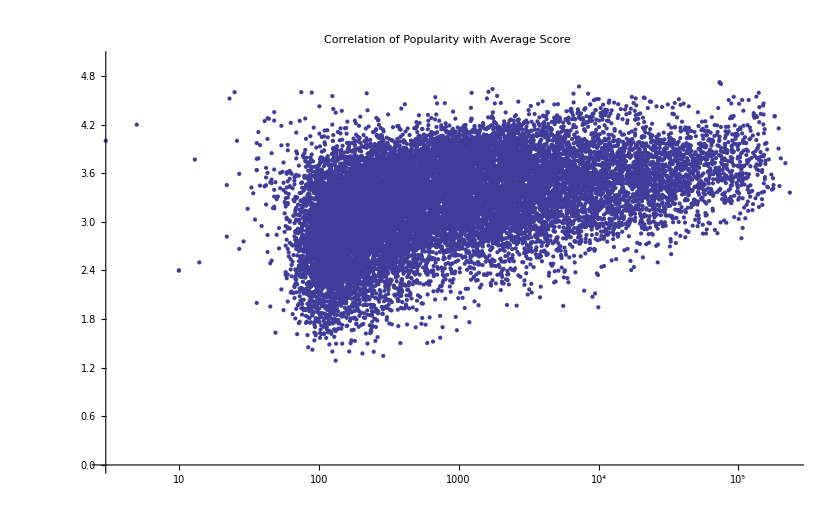

```mathematica
popplot=ListLogLinearPlot[srvp,PlotRange->{{0,250000},{0,5}},PlotLabel->"Correlation of Popularity with Average Score"]
```

```mathematica
popplot>>popplot;
```

```mathematica
reviews>>reviews;
```

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

```mathematica
sr=Sort[reviews,#2<#1&];
```

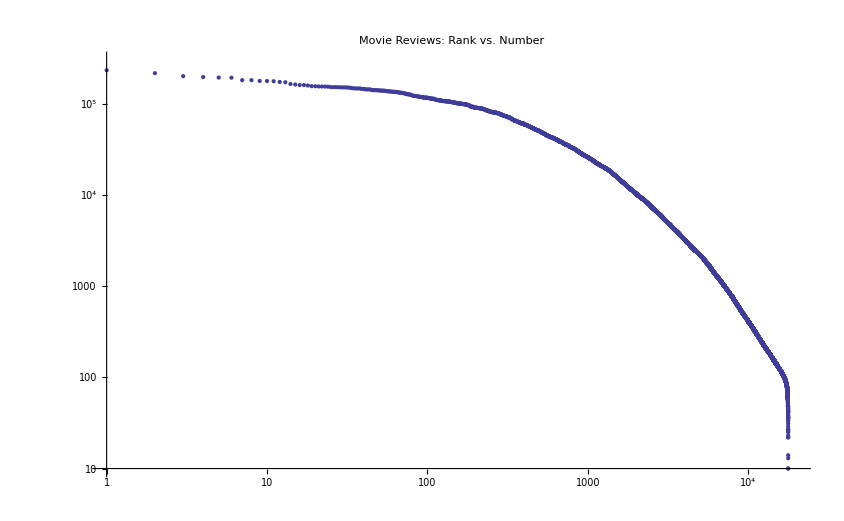

```mathematica
mrplot=ListLogLogPlot[Table[{i,sr[[i]]},{i,Length[sr]}],PlotRange->{{1,20000},{10,300000}},PlotLabel->"Movie Reviews:  Rank vs. Number"]
```

```mathematica
Dimensions[reviewspers]
```

{480183,2}

```mathematica
reviewspers[[1]]
```

{6,623}

```mathematica
peoplerevnums[x_]:={
a=0;
Do[If[reviewspers[[i,2]]≤x,a+=1],{i,Length[reviewspers]}];
a
}
```

```mathematica
peoplerevnums[100]
```

{245539}

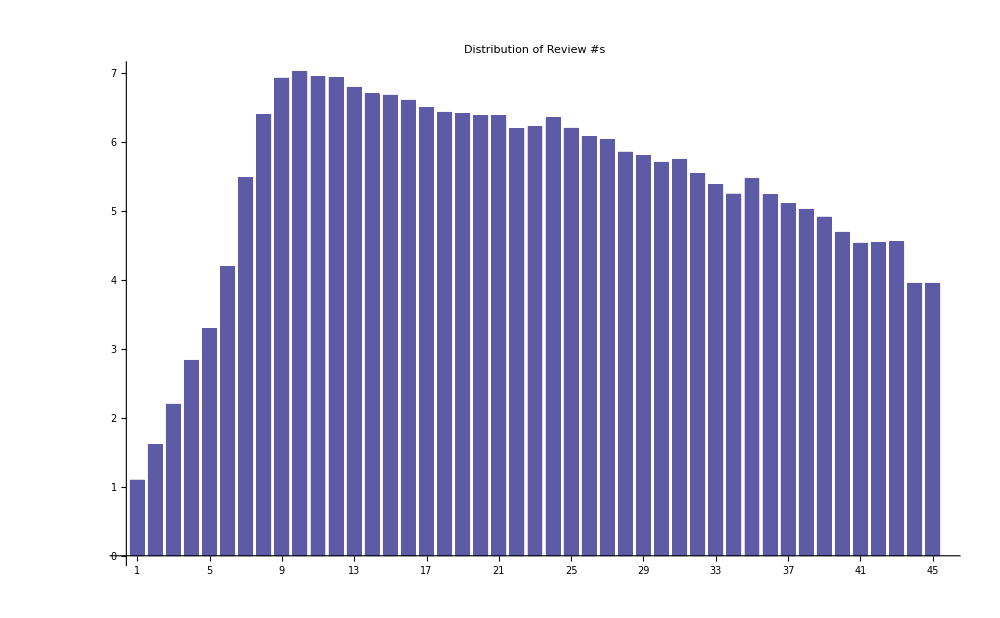

```mathematica
BarChart[Log[bclr],PlotLabel->"Distribution of Review #s"]
```

I believe the following stuff here is no longer used.

```mathematica
(*peopledist>>peopledist;*)
```

```mathematica
(*SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];
peopledist=Table[0,{3000000},{5}];
Do[
{
test=Get[pbmnames[[k]]];
Do[{
peopledist[[test[[i,j,2]],test[[i,j,3]]]]+=1,
If[IntegerQ[i/100000]==True,Print[i]]},
{i,1,Length[test]},{j,Length[test[[i]]]}
]
Clear[test];
},{k,1,6}
]*)
```

THe following tells how many reviews were published by each person, correlated with their personal id number.  The average is slightly more than 200 per person.   It also computes the distribution of scores for each person.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"];
avgdistpers=Table[0,{Length[people]},{5}];
reviewspers=Table[0,{Length[people]}];
Do[
{
test=Get[peoplefilenames[[j]]];
Do[
If[test[[i,2]]==k,avgdistpers[[j,k]]+=1],
{i,Length[test]},{k,1,5}
],
If[IntegerQ[j/1000]==True,Print[j]],
reviewspers[[j]]={people[[j]],Length[test]}
},{j,1,Length[peoplefilenames]}
]
```

```mathematica
Take[reviewspers,10]
```

{{6,623},{7,880},{8,98},{10,259},{25,27},{33,36},{42,128},{59,157},{79,795},{83,32}}

```mathematica
Mean[Table[reviewspers[[i,2]],{i,Length[reviewspers]}]]//N
```

208.675

```mathematica
Take[avgdistpers,10]
```

{{19,28,304,217,55},{5,33,221,308,313},{1,2,10,47,38},{8,46,80,85,40},{1,6,6,7,7},{1,2,4,27,2},{0,3,29,71,25},{15,13,27,50,52},{51,55,244,297,148},{0,1,7,16,8}}

Just check to see how many avgdistpers score vectors have zeroes in one or more places.  Use the Product function to project out zeroes.  It is almost 30%!! This is bad for linear analysis.

```mathematica
Length[DeleteCases[Table[Product[avgdistpers[[i,j]],{j,1,5}],{i,Length[people]}],0]]/Length[people]//N
```

0.705768

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
FileNames[]
```

{avgdist,avgdistpers,avgvector,avgvectorpers,cumreviewplot,.DS_Store,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavens,mrplot,personalmavs1,personalmavs10,personalmavs15,personalmavs5,personalmavslt5,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift}

```mathematica
spav=Sort[persavgvector];
```

The most movies that anybody ever reviewed.  Don't you have anything better to do with your life?

```mathematica
Max[Table[reviewspers[[i,2]],{i,Length[reviewspers]}]]
```

17583

```mathematica
avgdistpers>>avgdistpers;
```

```mathematica
reviewspers>>reviewspers;
```

```mathematica
persavgvector=Table[Sum[j avgdistpers[[i,j]],{j,5}]/reviewspers[[i,2]],{i,Length[avgdistpers]}]//N;
```

```mathematica
peoplepts=Table[{reviewspers[[i,2]],persavgvector[[i]]},{i,Length[people]}];
```

```mathematica
ListLogLinearPlot[peoplepts,PlotRange->{{0,20000},{0,5}},PlotLabel->"Correlation of Number of Reviews with Average Score"]
```

-Graphics-

```mathematica
%64>>plotrevbyscorebyperson;
```

```mathematica
MemoryInUse[]
```

327806784

```mathematica
parabola = Fit[peoplepts, {1,Log[x],(Log[x])^2}, x]
```

3.53779+0.096604 Log[x]-0.0134882 Log[x]^2

```mathematica
parabola>>revbyscorebypersonfit;
```

Reviewers get more jaded as they see more movies

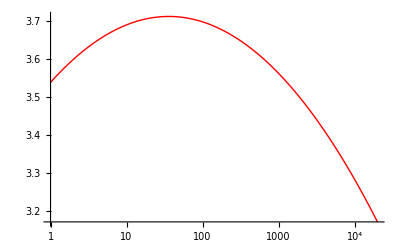

```mathematica
LogLinearPlot[parabola, {x,1,20000},PlotStyle->{Red, Thick}]
```

```mathematica
Show[%50,%63]
```

-Graphics-

```mathematica
Dimensions[reviewspers]
```

{480183,2}

```mathematica
reviewspers[[3]]
```

{8,98}

```mathematica
count[cutoff_]:=
{
ct=0;
Do[If[reviewspers[[i,2]]≥ cutoff,ct+=reviewspers[[i,2]]],{i,Length[ reviewspers]}];
ct
}[[1]]
```

```mathematica
count[2000]
```

3262629

```mathematica
cumreviews=Table[{2^(i/4),count[2^(i/4)]},{i,8,52}]
```

```mathematica
%119
```

{{4,100190716},{4 2^(1/4),100183728},{4 √2,100175208},{4 2^(3/4),100164972},{8,100152421},{8 2^(1/4),100117989},{8 √2,100066310},{8 2^(3/4),99987890},{16,99880664},{16 2^(1/4),99605091},{16 √2,99357682},{16 2^(3/4),98975833},{32,98447323},{32 2^(1/4),97619418},{32 √2,96697028},{32 2^(3/4),95626423},{64,94247386},{64 2^(1/4),92562976},{64 √2,90819688},{64 2^(3/4),88704334},{128,86224687},{128 2^(1/4),83136318},{128 √2,79597915},{128 2^(3/4),75514414},{256,70820447},{256 2^(1/4),65428498},{256 √2,59384891},{256 2^(3/4),52821864},{512,45853613},{512 2^(1/4),38400218},{512 √2,31003340},{512 2^(3/4),24093576},{1024,17830380},{1024 2^(1/4),12325837},{1024 √2,8118064},{1024 2^(3/4),5084412},{2048,3021995},{2048 2^(1/4),1852664},{2048 √2,1100437},{2048 2^(3/4),688540},{4096,497760},{4096 2^(1/4),355258},{4096 √2,281400},{4096 2^(3/4),174408},{8192,145714}}

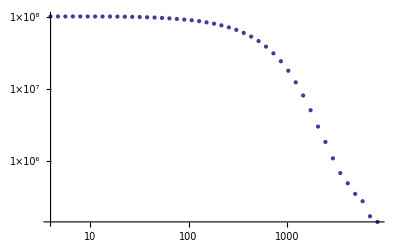

```mathematica
ListLogLogPlot[%]
```

```mathematica
Table[{1000 i, count2[1000i]},{i,232}];
```

```mathematica
sr=Sort[reviews];
```

```mathematica
sr[[17770]]
```

232944

```mathematica
Table[{177i,Plus@@Take[sr,-177 i]},{i,100}]
```

{{177,22499896},{354,36647019},{531,46475369},{708,53825760},{885,59673827},{1062,64392519},{1239,68309574},{1416,71678555},{1593,74502372},{1770,76882395},{1947,78922368},{2124,80704848},{2301,82292649},{2478,83704996},{2655,84953103},{2832,86076300},{3009,87086005},{3186,87992982},{3363,88818391},{3540,89568470},{3717,90258831},{3894,90891206},{4071,91472586},{4248,92008858},{4425,92505888},{4602,92966280},{4779,93399526},{4956,93807233},{5133,94189449},{5310,94548862},{5487,94883853},{5664,95195642},{5841,95487250},{6018,95756770},{6195,96007535},{6372,96242861},{6549,96464470},{6726,96673273},{6903,96870135},{7080,97055006},{7257,97229335},{7434,97393651},{7611,97548613},{7788,97694786},{7965,97833401},{8142,97963779},{8319,98086162},{8496,98201736},{8673,98310950},{8850,98414568},{9027,98512339},{9204,98605448},{9381,98693872},{9558,98778034},{9735,98858252},{9912,98934991},{10089,99008103},{10266,99078072},{10443,99145049},{10620,99208957},{10797,99270162},{10974,99328583},{11151,99384564},{11328,99438137},{11505,99489453},{11682,99538576},{11859,99585593},{12036,99630669},{12213,99674059},{12390,99715793},{12567,99755861},{12744,99794491},{12921,99831851},{13098,99867852},{13275,99902637},{13452,99936338},{13629,99968898},{13806,100000418},{13983,100030807},{14160,100060150},{14337,100088479},{14514,100115914},{14691,100142457},{14868,100168095},{15045,100193000},{15222,100217087},{15399,100240426},{15576,100263043},{15753,100284950},{15930,100306226},{16107,100326904},{16284,100346973},{16461,100366325},{16638,100384981},{16815,100402898},{16992,100420058},{17169,100436367},{17346,100451719},{17523,100465812},{17700,100477750}}

```mathematica
srp=Sort[Table[reviewspers[[i,2]],{i,Length[reviewspers]}]];
```

```mathematica
srp[[-1]]
```

17583

```mathematica
interval=Floor[Length[srp]/100];
Table[{i interval, Plus@@Take[srp, -interval i]},{i,100}]
```

{{4801,9086789},{9602,15003598},{14403,19964771},{19204,24319523},{24005,28231088},{28806,31793966},{33607,35074709},{38408,38120041},{43209,40965866},{48010,43635976},{52811,46147714},{57612,48516781},{62413,50755067},{67214,52874754},{72015,54887379},{76816,56801925},{81617,58623242},{86418,60358103},{91219,62011495},{96020,63591031},{100821,65100082},{105622,66544143},{110423,67926147},{115224,69249278},{120025,70516597},{124826,71730517},{129627,72895272},{134428,74013684},{139229,75087361},{144030,76118456},{148831,77109347},{153632,78061904},{158433,78977229},{163234,79856074},{168035,80700113},{172836,81511737},{177637,82291896},{182438,83042223},{187239,83763894},{192040,84458293},{196841,85126099},{201642,85768607},{206443,86386421},{211244,86981176},{216045,87553263},{220846,88103506},{225647,88632838},{230448,89141597},{235249,89630988},{240050,90101859},{244851,90555247},{249652,90991297},{254453,91410947},{259254,91814912},{264055,92203574},{268856,92577492},{273657,92937606},{278458,93284486},{283259,93618788},{288060,93940718},{292861,94251229},{297662,94550317},{302463,94839162},{307264,95118324},{312065,95388303},{316866,95649054},{321667,95900858},{326468,96143430},{331269,96377515},{336070,96603602},{340871,96821678},{345672,97031609},{350473,97234789},{355274,97429870},{360075,97618560},{364876,97799499},{369677,97974167},{374478,98141332},{379279,98301961},{384080,98456158},{388881,98603436},{393682,98744704},{398483,98879794},{403284,99008177},{408085,99130846},{412886,99247752},{417687,99358848},{422488,99463425},{427289,99562391},{432090,99655745},{436891,99743398},{441692,99825032},{446493,99900524},{451294,99970306},{456095,100033742},{460896,100089267},{465697,100135791},{470498,100170648},{475299,100192486},{480100,100202276}}

```mathematica
Max[reviews]
```

232944

```mathematica
FileNames[]
```

{1000,avgdist,avgdistpers,avgvector,avgvectorpers,grandaveragebyperson,grandaveragebyreview,mrplot,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift}

```mathematica
%120>>cumreviewplot;
```

```mathematica
%119>cumreviewnums;
```

## Da Bomb

Here's the first plan.  I call it "Ever So Much More So".  The whole world of movies has an average review score - - about 3.7.  Each movie has a time dependent average score.  Each person has a personal average of all of their reviews --  Some seem to be optimists, some pessimists in relation to the grand average score.  Then people have their own personal dynamic range:  How good is "good" and how bad is "bad"?  So I will start with a person's average rating of all movies as their "personal setpoint"--the center of their particular distribution.  Then I will look at the rating of a particular movie m_i in relation to the grand average score.  Consider this difference, plus or minus.  Multiply it by the personal standard deviation (s_j) and a tuneable multiplicative parameter mu  (strength of coupling to other people's opinions, after the Lux model)  I will tune mu to minimize the overall standard deviaiton of the Grand Prediction.

Note:  The "personal deviation" idea didn't work, though the personal setpoint did.  Neither of them are good enough to beat Cinematch, rather just tie it.

### Load everything in

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles

```mathematica
FileNames[]
```

{BulkStats,.DS_Store,PeopleByMovies,peopleids,probe,probescores,probesorted,probesortsample,synqual,TestFolder,titles,TrainingMma}

```mathematica
psf=Flatten[probescores,1];
```

```mathematica
Dimensions[psf]
```

{1408395,4}

```mathematica
probescores[[1]]
```

{{1,30878,4,3281},{1,2647871,4,3285},{1,1283744,3,2663},{1,2488120,5,3184},{1,317050,5,3240},{1,1904905,4,3054},{1,1989766,4,3110},{1,14756,4,3282},{1,1027056,3,3258},{1,1149588,4,3268},{1,1394012,5,3274},{1,1406595,4,3160},{1,2529547,5,3243},{1,1682104,4,3163},{1,2625019,3,3176},{1,2603381,5,3254},{1,1774623,4,3248},{1,470861,5,2735},{1,712610,4,3038},{1,1772839,5,3183},{1,1059319,3,3204},{1,2380848,5,2932},{1,548064,5,3257}}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

```mathematica
FileNames[]
```

{avgdist,avgdistpers,avgvector,avgvectorpers,cumreviewplot,.DS_Store,grandaveragebyperson,grandaveragebyreview,knesset,mavenmatrix,mavens,mrplot,newmavenmatrix,personalmavens,personalmavens2,personalstdev,plotrevbyscorebyperson,pmavs,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift,supermavenmatrix}

```mathematica
peoplefilenames=Table[StringJoin["personfile",ToString[people[[i]]]],{i,Length[people]}];
```

```mathematica
reversepersontable=Table[0,{2649429}];
Do[reversepersontable[[people[[i]]]]=i,{i,Length[people]}]
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize"]
```

/Users/brucesawhill/Desktop/NetFlixPrize

### The score predictor (person x movie x date)

```mathematica
avgtimescore[movie_,date_]:=seculardrift[[movie,1]]+date seculardrift[[movie,2]];
```

```mathematica
predictedscore[movie_,date_,personid_]:=
{
pospers=reversepersontable[[personid]];
av=avgvector[[movie]];
(*av=avgtimescore[movie,date];*)
persoffset= avgvectorpers[[pospers]]-3.67419;
score=av+persoffset
}
```

```mathematica
Take[people,-3]
```

{2649421,2649426,2649429}

```mathematica
avgvector[[1]]
```

3.74954

```mathematica
psf[[1]]
```

{1,30878,4,3281}

```mathematica
predict1=Table[predictedscore[psf[[i,1]],psf[[i,4]],psf[[i,2]]][[1]],{i,Length[psf]}];//Timing
```

{12.3621,Null}

```mathematica
Dimensions[predict1]
```

{1408395}

```mathematica
Do[If[predict1[[i]]>5.0,predict1[[i]]=5.0],{i,Length[predict1]}];
Do[If[predict1[[i]]<1.0,predict1[[i]]=1.0],{i,Length[predict1]}];
```

```mathematica
devs=Table[predict1[[i]]-psf[[i,3]],{i,Length[psf]}];
```

```mathematica
devs[[1]]
```

-0.289628

```mathematica
Take[devs,30]
```

{-0.289628,-0.692415,0.616337,-0.266262,-1.27949,-0.0755904,-0.591314,-0.281546,1.05313,-0.461932,-2.01418,-0.389763,-1.00814,0.0173819,-0.197374,-0.99507,-0.395716,-0.470102,0.152276,-0.797663,0.0961863,0.,-1.4537,-0.0818649,-0.347288,0.207243,-0.102101,0.610021,-0.389979,-1.25536}

```mathematica
dev2=Sum[devs[[i]]^2,{i,Length[psf]}]
```

1.32886×10^6

```mathematica
rms=Sqrt[dev2/Length[psf]]
```

0.971354

```mathematica
MemoryInUse[]
```

693218240

## The Knesset

The next try is to use the Maven idea.  Notice that the variance of average scores tightens up for more experienced reviewers.  The sweet spot seems to be people who have reviewed between 1k and 2k movies.  More than that the cumulative reviews/reviewers curve takes a departure from Gaussian, which might imply professionals or organizations reviewing movies.  I think the results will be better with "ordinary people" who just watch a lot of movies, in the style of the Zagat.  This needs to be small enough subset so that it is a small perturbation of the whole, maybe 1%.  But it needs to be big enough to give the vast majority of movies good coverage, maybe 95 - 99%.  This is probably in the 1M to 10M range of total reviews, maybe 1000 mavens.    Almost all movies have 100 reviews or more, so 1M randomly distributed reviews will do ok, providing rare movies with a 1/e probability of 1 review.

```mathematica
FileNames[]
```

{avgbymovie,avgbyperson,cumreviewplot,distbymovie,distbymoviemp,distbyperson,distbypersonmp,.DS_Store,fastknesset,grandaveragebyperson,grandaveragebyreview,MavenAnalysis,mavencitizenmatrix,mavenmatrix,mavens,meanfieldmodel,mrplot,NaNmavendensity,peopleids,plotrevbyscorebyperson,popplot,revbyscorebypersonfit,reversepersontable,reviews,reviewsmp,reviewspers,reviewspersmp,seculardrift,titles,top40}

```mathematica
mavens=DeleteCases[Table[If[reviewspers[[i,2]]≥1500 && reviewspers[[i,2]]≤4000,reviewspers[[i]],0],{i,1,Length[reviewspers]}],0];
```

```mathematica
mavens>>mavens;
```

```mathematica
mavens=<<mavens;
```

```mathematica
mavens[[2333]]
```

{1730699,1519}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
FileNames[]
```

{avgbymovie,cumreviewplot,distbymovie,distbymoviemp,distbypeoplemp,distbyperson,.DS_Store,fastknesset,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavens,mrplot,peopleids,plotrevbyscorebyperson,popplot,revbyscorebypersonfit,reversepersontable,reviews,reviewsmp,reviewspers,reviewspersmp,seculardrift,titles}

```mathematica
Dimensions[mavens]
```

{3571,2}

```mathematica
people=<<peopleids;
```

```mathematica
Dimensions[people]
people[[-1]]
```

{480189}

2649429

```mathematica
reversepersontable=<<reversepersontable;
```

```mathematica
reversepersontable=Table[0,{2649429}];
Do[reversepersontable[[people[[i]]]]=i,{i,Length[people]}];
reversepersontable>>reversepersontable;
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMoviesMinusProbe"];
```

```mathematica
mavenmatrix=Table[0,{Length[mavens]}];
Do[mavenmatrix[[i]]=getfile[reversepersontable[[mavens[[i,1]]]]],{i,Length[mavens]}];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

```mathematica
mavenmatrix>>mavenmatrix;
```

```mathematica
mavenmatrix=<<mavenmatrix;
```

```mathematica
Dimensions[Flatten[mavenmatrix,1]]
```

{6927543,4}

```mathematica
MemoryInUse[]
```

71094384

Old size of mavenmatrix before I made it out of PbM-P.  I don't know what it's different, especially bigger instead of smaller.  Maybe some of the missing people were mavens.

```mathematica
{6916834,3}
```

```mathematica
getfile[personnumber_]:=
{
aa=Get[peoplefilenames[[personnumber]]];
aa
}[[1]]
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies

```mathematica
compare[file1_,file2_]:=
{
(*Print["First file has ", Length[file1] ," entries and second file has ", Length[file2], " entries."];*)
movies1=Table[file1[[i,4]],{i,Length[file1]}];
movies2=Table[file2[[i,4]],{i,Length[file2]}];
commons=Intersection[movies1,movies2];
(*Print["There are ", Length[commons], " movies in common"];*)
{Length[commons]/Min[Length[movies1],Length[movies2]],tastehamming[movies1,movies2,file1,file2,commons]}
}[[1]]
```

```mathematica
tastehamming[movienums1_,movienums2_,file1_,file2_,commonmovienums_]:=
{
avector=Table[file1[[Position[movienums1,commonmovienums[[j]]][[1,1]]]][[2]],{j,Length[commonmovienums]}];
bvector=Table[file2[[Position[movienums2,commonmovienums[[j]]][[1,1]]]][[2]],{j,Length[commonmovienums]}];
avga=Mean[avector]//N;
avgb=Mean[bvector]//N;
stdeva=If[Length[avector]≥2,StandardDeviation[avector]//N,1];
stdevb=If[Length[bvector]>2,StandardDeviation[bvector]//N,1];
If[stdeva≤.5,stdeva=.5];
If[stdevb≤.5,stdevb=.5];
(*Print["stdeva = ",stdeva];
Print["stdevb = ",stdevb];
Print["avga = ", avga];
Print["avgb = ",avgb];*)
th=(avector-avga)stdevb/stdeva+avgb-bvector;
If[Length[th]≥2,StandardDeviation[th],1]//N
}[[1]]
```

```mathematica
compare[getfile[1],getfile[2]]
```

First file has 626 entries and second file has 881 entries.

There are 283 movies in common

{283/626,1.09857}

{74.8837,Null}

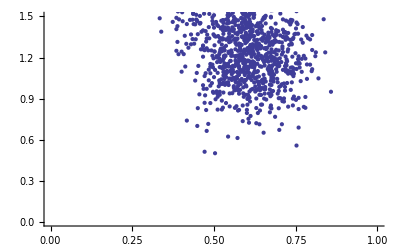

```mathematica
blab=Table[compare[getfile[1],mavenmatrix[[k]]],{k,1000}];//Timing
ListPlot[blab,PlotRange->{{0,1},{0,1.5}}]
```

```mathematica
Length[getfile[reversepersontable[[2647888]]]]
```

1564

```mathematica
fillout[file_]:=
{filledout=Table[0,{17770}];
Do[filledout[[file[[j,1]]]]=file[[j,2]],{j,Length[file]}];
filledout
}
```

```mathematica
fillout[supermavenmatrix[[1]]];//Timing
```

{0.010642,Null}

```mathematica
mavencompare[file1_,file2_]:=
{fillout[file1];
veca=DeleteCases[Table[filledout[[file2[[i,1]]]],{i,Length[file2]}],0];
mva=Mean[veca];
vecb=DeleteCases[Table[If[filledout[[file2[[i,1]]]]==0,0, file2[[i,2]]],{i,Length[file2]}],0];
mvb=Mean[vecb];
Clear[filledout];
stdeva=If[Length[veca]≥2,StandardDeviation[veca]//N,1];
stdevb=If[Length[vecb]>2,StandardDeviation[vecb]//N,1];
If[stdeva≤.3,stdeva=.3];
If[stdevb≤.3,stdevb=.3];
th=(veca-mva)stdevb/stdeva+mvb-vecb;
If[Length[th]≥2,StandardDeviation[th],1]//N
}[[1]]
```

```mathematica
mavencompare[supermavenmatrix[[1]],getfile[4]]//Timing
```

{0.020584,1.40657}

```mathematica
compare[supermavenmatrix[[1]],getfile[4]]//Timing
```

{0.116256,1.40657}

## MavenMod

This is a modified maven idea where the predictor is based on disaggregating the fitting process so that non-linear and even non-functional forms can be fitted.  Instead of one fit of the form (a x + b) there is a hash table saying what each maven integer value corresponds to in terms of average citizen score.  The total prediction is made by averaging over the maven hits (citizen scores predicted from maven scores that are only counted when the mavens saw the movie in question)   This should atually be faster than least squares curve fitting because much less computation is involved--just addition and subtraction instead of matrix processes.  This may allow the basis of support to be sufficiently enlarged such that a significant improvement in prediction is found, in addition to the nonlinear benefits.

Note that the following function is asymmetric, it uses the first vector as the basis and the second as the dependent variable for prediction.  In practical usage, the first one will be the "maven", the second one will be the "citizen".

```mathematica
varcompare[file1_,file2_]:=
{
Print["The first file has ", Length[file1] ," entries and second file has ", Length[file2], " entries."];
movies1=Table[file1[[i,4]],{i,Length[file1]}];
movies2=Table[file2[[i,4]],{i,Length[file2]}];
commons=Intersection[movies1,movies2];
Print["There are ", Length[commons], " movies in common"];
overlap=Length[commons]/Min[Length[movies1],Length[movies2]];
stepvariance2[movies1,movies2,file1,file2,commons]
}[[1]]
```

```mathematica
stepvariance2[movienums1_,movienums2_,file1_,file2_,commonmovienums_]:=
{
pairs=Table[{file1[[Position[movienums1,commonmovienums[[j]]][[1,1]]]][[2]],file2[[Position[movienums2,commonmovienums[[j]]][[1,1]]]][[2]]},{j,Length[commonmovienums]}];
fivevector=Table[{},{5}];
Do[AppendTo[fivevector[[pairs[[i,1]]]],pairs[[i]]],{i,Length[pairs]}];
fivemean=Table[0,{5}];
Do[fivemean[[i]]=If[fivevector[[i]]≠{},{Sum[fivevector[[i,j,2]],{j,Length[fivevector[[i]]]}]/Length[fivevector[[i]]]//N,Length[fivevector[[i]]]},"NaN"],{i,5}];
fivevariance=Table[0,{5}];
Do[fivevariance[[i]]=If[Length[fivevector[[i]]]≥2,Sqrt[ Sum[(fivevector[[i,j,2]]-fivemean[[i,1]])^2,{j,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-1)],"NaN"],{i,5}]
}
```

```mathematica
compvarcompare=Compile[
{{file1, _Integer,2},{file2, _Integer,2}},
(*Print["The first file has ", Length[file1] ," entries and second file has ", Length[file2], " entries."];*)
movies1=Table[file1[[i,4]],{i,Length[file1]}];
movies2=Table[file2[[i,4]],{i,Length[file2]}];
commons=Intersection[movies1,movies2];
If[commons=={},commons={0}];
(*Print["There are ", Length[commons], " movies in common"];*)
overlap=If[commons≠{0},Length[commons]/Min[Length[movies1],Length[movies2]],0];
compstepvariance2[movies1,movies2,file1,file2,commons];
]
```

CompiledFunction[{file1,file2},movies1=Table[file1⟦i,4⟧,{i,Length[file1]}];movies2=Table[file2⟦i,4⟧,{i,Length[file2]}];commons=movies1∩movies2;If[commons=={},commons={0}];overlap=If[commons≠{0},Length[commons]/Min[Length[movies1],Length[movies2]],0];compstepvariance2[movies1,movies2,file1,file2,commons];,-CompiledCode-]

```mathematica
compstepvariance2=Compile[
{{movienums1,_Integer,1},{movienums2, _Integer, 1}, {file1, _Integer,2},
{file2, _Integer,2},{commonmovienums, _Integer, 1}},
pairs=Table[{file1[[Position[movienums1,commonmovienums[[j]]][[1,1]]]][[2]],file2[[Position[movienums2,commonmovienums[[j]]][[1,1]]]][[2]]},{j,Length[commonmovienums]}];
fivevector=Table[{},{5}];
Do[AppendTo[fivevector[[pairs[[i,1]]]],pairs[[i]]],{i,Length[pairs]}];
fivemean=Table[{0,0},{5}];
Do[fivemean[[i]]=If[fivevector[[i]]≠{},{Sum[fivevector[[i,j,2]],{j,Length[fivevector[[i]]]}]/Length[fivevector[[i]]]//N,Length[fivevector[[i]]]},{0,0}],{i,5}];
fivevariance=Table[0,{5}];
Do[fivevariance[[i]]=If[Length[fivevector[[i]]]≥2,Sqrt[ Sum[(fivevector[[i,j,2]]-fivemean[[i,1]])^2,{j,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-1)],"NaN"],{i,5}];
]
```

CompiledFunction[{movienums1,movienums2,file1,file2,commonmovienums},pairs=Table[{file1⟦Position[movienums1,commonmovienums⟦j⟧]⟦1,1⟧⟧⟦2⟧,file2⟦Position[movienums2,commonmovienums⟦j⟧]⟦1,1⟧⟧⟦2⟧},{j,Length[commonmovienums]}];fivevector=Table[{},{5}];Do[AppendTo[fivevector⟦pairs⟦i,1⟧⟧,pairs⟦i⟧],{i,Length[pairs]}];fivemean=Table[{0,0},{5}];Do[fivemean⟦i⟧=If[fivevector⟦i⟧≠{},{N[(∑_(j=1)^Length[fivevector⟦i⟧] fivevector⟦i,j,2⟧)/Length[fivevector⟦i⟧]],Length[fivevector⟦i⟧]},{0,0}],{i,5}];fivevariance=Table[0,{5}];Do[fivevariance⟦i⟧=If[Length[fivevector⟦i⟧]≥2,√((∑_(j=1)^Length[fivevector⟦i⟧] (fivevector⟦i,j,2⟧-fivemean⟦i,1⟧)^2)/(Length[fivevector⟦i⟧]-1)),NaN],{i,5}];,-CompiledCode-]

```mathematica
sdf={{}}
```

{{}}

```mathematica
lp=If[sdf≠{{}},Length[sdf],0];
```

```mathematica
lp
```

0

```mathematica
Length[sdf]
```

1

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies

```mathematica
Timing[varcompare[getfile[reversepersontable[[mavens[[1,1]]]]],getfile[2]]]
```

The first file has 2982 entries and second file has 881 entries.

There are 624 movies in common

{0.136525,{Null}}

```mathematica
fivemean
```

{{3.47778,90},{3.7644,191},{4.30151,199},{4.53448,116},{4.60714,28}}

```mathematica
fivevariance
```

{0.87702,0.941438,0.765116,0.596089,0.737327}

```mathematica
Timing[compvarcompare[getfile[reversepersontable[[mavens[[1,1]]]]],getfile[2]]]
```

{0.082266,Null}

```mathematica
Timing[compvarcompare[mavenmatrix[[1]],getfile[2]]]
```

{0.060576,Null}

```mathematica
fivemean
```

{{3.47778,90},{3.7644,191},{4.30151,199},{4.53448,116},{4.60714,28}}

```mathematica
fivevariance
```

{0.87702,0.941438,0.765116,0.596089,0.737327}

This works for the mavenfiles made into vectors 17 770 elements long.

```mathematica
fastvarcompare[mavenfile1_,file2_]:=
{
(*Print["The first file has ", Length[DeleteCases[mavenfile1,0]] ," entries and second file has ", Length[file2], " entries."];*)
(*movies1=Table[file1[[i,1]],{i,Length[file1]}];
movies2=Table[file2[[i,1]],{i,Length[file2]}];*)
mavencommonscorevector=Table[If[mavenfile1[[file2[[i,1]]]]==0,{0,0},{file2[[i,2]],mavenfile1[[file2[[i,1]]]]}],{i,Length[file2]}];
mavencommonscorevector=DeleteCases[mavencommonscorevector,{0,0}];
stepvariance2go[mavencommonscorevector];
(*Print["There are ", Length[mavencommonscorevector], " movies in the citizen file"];*)
(*overlap=Length[commons]/Min[Length[movies1],Length[movies2]];*)
(*stepvariance2[movies1,movies2,mavenfile1,file2,commons]*)
}
```

```mathematica
cfvc=
Compile[
{{mavenfile1,_Integer,1},{file2,_Integer,2}},
mavencommonscorevector=
Table[
If[
mavenfile1[[file2[[i,1]]]]==0,{0,0},{file2[[i,2]],mavenfile1[[file2[[i,1]]]]}
],{i,Length[file2]}
];
mavencommonscorevector=DeleteCases[mavencommonscorevector,{0,0}];
stepvariance2go[mavencommonscorevector];
(*Print["There are ", Length[mavencommonscorevector], " movies in common."];*)
]
```

```mathematica
stepvariance[movienums1_,movienums2_,file1_,file2_,commonmovienums_]:=
{
avector=Table[file1[[Position[movienums1,commonmovienums[[j]]][[1,1]]]][[2]],{j,Length[commonmovienums]}];
bvector=Table[file2[[Position[movienums2,commonmovienums[[j]]][[1,1]]]][[2]],{j,Length[commonmovienums]}];
(*Print["avector = ",Length[avector]],
Print["bvector = ",Length[bvector]],*)
pairs=Table[{avector[[i]],bvector[[i]]},{i,Length[avector]}];
fivevector=Table[{},{5}];
Do[AppendTo[fivevector[[pairs[[i,1]]]],pairs[[i]]],{i,Length[pairs]}];
fivemean=Table[0,{5}];
Do[fivemean[[i]]=If[fivevector[[i]]≠{},{Sum[fivevector[[i,j,2]],{j,Length[fivevector[[i]]]}]/Length[fivevector[[i]]]//N,Length[fivevector[[i]]]},"NaN"],{i,5}];
(*Print["fivemean = ",fivemean];*)
(*ListPlot[Table[{i,fivemean[[i,1]]},{i,5}],PlotJoined->True],*)
fivevariance=Table[0,{5}];
Do[fivevariance[[i]]=If[Length[fivevector[[i]]]≥2,Sqrt[ Sum[(fivevector[[i,j,2]]-fivemean[[i,1]])^2,{j,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-1)],"NaN"],{i,5}],
(*Print["fivevariance = ", fivevariance];*)
}
```

```mathematica
stepvariance2go[pairs_]:=
{
fivevector=Table[{},{5}];
Do[AppendTo[fivevector[[pairs[[i,1]]]],pairs[[i]]],{i,Length[pairs]}];
fivemean=Table[0,{5}];
Do[fivemean[[i]]=If[fivevector[[i]]≠{},{Sum[fivevector[[i,j,2]],{j,Length[fivevector[[i]]]}]/Length[fivevector[[i]]]//N,Length[fivevector[[i]]]},"NaN"],{i,5}];
fivevariance=Table[0,{5}];
Do[fivevariance[[i]]=If[Length[fivevector[[i]]]≥2,Sqrt[ Sum[(fivevector[[i,j,2]]-fivemean[[i,1]])^2,{j,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-1)],"NaN"],{i,5}]
}
```

```mathematica
stepvariance2goprime[pairs_]:=
{
fivevector=Table[{{0,0}},{5}];
Do[AppendTo[fivevector[[pairs[[i,1]]]],pairs[[i]]],{i,Length[pairs]}];
fivemean=Table[0,{5}];
Do[fivemean[[i]]=If[fivevector[[i]]≠{0,0},{Sum[fivevector[[i,j,2]],{j,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-1)//N,Length[fivevector[[i]]]-1},"NaN"],{i,5}];
fivevariance=Table[0,{5}];
Do[fivevariance[[i]]=If[Length[fivevector[[i]]]≥2,Sqrt[ Sum[(fivevector[[i,j,2]]-fivemean[[i,1]])^2,{j,2,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-2)],"NaN"],{i,5}]
}
```

```mathematica
csv2g=Compile[{{pairs,_Integer,2}},
{
fivevector=Table[{0,0},{5}];
Do[AppendTo[fivevector[[pairs[[i,1]]]],pairs[[i]]],{i,Length[pairs]}];
fivemean=Table[0,{5}];
Do[fivemean[[i]]=If[fivevector[[i]]≠{{0,0}},{Sum[fivevector[[i,j,2]],{j,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-1)//N,Length[fivevector[[i]]]-1},"NaN"],{i,5}];
fivevariance=Table[0,{5}];
Do[fivevariance[[i]]=If[Length[fivevector[[i]]]≥2,Sqrt[ Sum[(fivevector[[i,j,2]]-fivemean[[i,1]])^2,{j,2,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-2)],"NaN"],{i,5}]
}
]
```

Compile::cptype: List is not supported for type "Void"; evaluation will use the uncompiled function.

CompiledFunction[{pairs},{fivevector=Table[{0,0},{5}];Do[AppendTo[fivevector⟦pairs⟦i,1⟧⟧,pairs⟦i⟧],{i,Length[pairs]}];fivemean=Table[0,{5}];Do[fivemean⟦i⟧=If[fivevector⟦i⟧≠{{0,0}},{N[(∑_(j=1)^Length[fivevector⟦i⟧] fivevector⟦i,j,2⟧)/(Length[fivevector⟦i⟧]-1)],Length[fivevector⟦i⟧]-1},7],{i,5}];fivevariance=Table[0,{5}];Do[fivevariance⟦i⟧=If[Length[fivevector⟦i⟧]≥2,√((∑_(j=2)^Length[fivevector⟦i⟧] (fivevector⟦i,j,2⟧-fivemean⟦i,1⟧)^2)/(Length[fivevector⟦i⟧]-2)),7],{i,5}]},-CompiledCode-]

About a factor of three speedup over the uncompiled code, which is itself a lot faster than the original.  Overall speedup about a factor of 15-25!!  Getting the compare-to file 225 times slows things down quite a lot.  I think there must be some nonlinearity here, uncompiled code is faster for little files, much slower for big ones.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"]
Timing[Table[fastvarcompare[mavenmoviematrix225[[i]],getfile[2]],{i,1,225}];]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder

{9.21492,Null}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"]
a=getfile[2];
Timing[Table[fastvarcompare[mavenmoviematrix225[[i]],a],{i,1,225}];]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder

{8.02872,Null}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"]
a=getfile[2];
Timing[Table[cfvc[mavenmoviematrix225[[i]],a],{i,1,225}];]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder

{1.36617,Null}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"]
Timing[Table[cfvc[mavenmoviematrix225[[i]],getfile[2]],{i,1,225}];]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder

{2.33216,Null}

```mathematica
Timing[varcompare[getfile[2],getfile[reversepersontable[[mavens[[mavens225[[2]],1]]]]]]]
fivemean
fivevariance
```

The first file has 880 entries and second file has 1606 entries.

{0.086074,{Null}}

{{3.5,2},{2.71429,7},{3.01351,74},{3.46939,147},{3.85106,188}}

{0.707107,0.755929,1.11642,1.02907,0.996866}

```mathematica
Timing[fastvarcompare[mavenmoviematrix225[[2]],getfile[2]]]
fivemean
fivevariance
```

{0.051009,{Null}}

{{3.5,2},{2.71429,7},{3.01351,74},{3.46939,147},{3.85106,188}}

{0.707107,0.755929,1.11642,1.02907,0.996866}

```mathematica
Timing[cfvc[mavenmoviematrix225[[2]],getfile[2]]]
fivemean
fivevariance
```

{0.014416,Null}

{{3.5,2},{2.71429,7},{3.01351,74},{3.46939,147},{3.85106,188}}

{0.707107,0.755929,1.11642,1.02907,0.996866}

### The search for mavens

This makes a single huge file which evidently cannot even be read by OpenRead[]

```mathematica
mavensearch[citizenno_,mavenno_]:=
{
Do[
{
statvector=Table[{},{mavenno}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];compvarcompare[mavenmatrix[[i]],getfile[j]];
dataconstruct=Table[{fivemean[[i,2]],{fivemean[[i,1]],fivevariance[[i]]}},{i,5}];
dataconstruct=Join[{{i,j,overlap}},{dataconstruct}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats/MavenSearch"];
dataconstruct>>>mavensearch2;
(*Clear[fivemean];
Clear[fivevariance];
Clear[fivevector]*)
Clear[overlap,commons,movies1,movies2,aa,dataconstruct];
If[IntegerQ[(i citizenno + j)/10000]==True,Print[i citizenno + j]];
},
{i,mavenno},{j,citizenno}
];
}
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats/MavenAnalysis"];
```

Here's a version that puts the results for each maven into its own file

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
people=<<peopleids;
```

```mathematica
peoplefilenames=Table[StringJoin["personfile",ToString[people[[i]]]],{i,Length[people]}];
```

```mathematica
reversepersontable=Table[0,{2649429}];
Do[reversepersontable[[people[[i]]]]=i,{i,Length[people]}];
reversepersontable>>reversepersontable;
```

```mathematica
getfile[personnumber_]:=
{
aa=Get[peoplefilenames[[personnumber]]];
aa
}[[1]]
```

```mathematica
mavens=<<mavens;
```

```mathematica
mavenmatrix=<<mavenmatrix;
```

```mathematica
mavensearch2[citizenno_,mavenno_]:=
{
Do[
{
statvector=Table[{},{citizenno}];
name=StringJoin["mavensearch",ToString[i]];
Do[
{
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];compvarcompare[mavenmatrix[[i]],getfile[j]];
dataconstruct=Table[{fivemean[[m,2]],{fivemean[[m,1]],fivevariance[[m]]}},{m,5}];
dataconstruct=Join[{{i,j,overlap}},{dataconstruct}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats/MavenAnalysis2"];
statvector[[j]]=dataconstruct;
Clear[overlap,commons,movies1,movies2,aa,dataconstruct,fivemean,fivevariance,fivevector,pairs];
If[IntegerQ[((i-1) citizenno + j)/1000]==True,Print[i citizenno + j]];
},
{j, citizenno}
];
PutAppend[statvector,name];
Clear[statvector];
},{i,1,mavenno}
];
}
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/PeopleByMovies"];
```

```mathematica
compvarcompare[mavenmatrix[[1]],getfile[6]];
```

The big grind, takes a day

```mathematica
mavensearch2[2000,3571]
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats/MavenAnalysis"];
```

```mathematica
lp=Table[0,{3571}];
Do[
{
name=StringJoin["mavensearch",ToString[i]];
currentfile=Get[name];
flat=Flatten[currentfile];
lp[[i]]=Length[Position[flat,"NaN"]];
Clear[currentfile,flat];
If[IntegerQ[i/100]==True,Print[i]]
},{i,3571}
]
```

Investigate the results some

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
FileNames[]
```

{avgbymovie,cumreviewplot,distbymovie,distbymoviemp,distbypeoplemp,distbyperson,.DS_Store,fastknesset,grandaveragebyperson,grandaveragebyreview,MavenAnalysis,mavencitizenmatrix,mavenmatrix,mavens,mrplot,NaNmavendensity,peopleids,plotrevbyscorebyperson,popplot,revbyscorebypersonfit,reversepersontable,reviews,reviewsmp,reviewspers,reviewspersmp,seculardrift,titles}

```mathematica
mavens=<<mavens;
```

```mathematica
nans=<<NaNmavendensity;
```

```mathematica
lp>>NaNmavendensity;
```

```mathematica
Needs["Histograms`"]
```

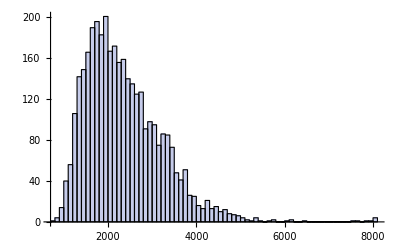

```mathematica
Histogram[lp]
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
mavenscoremat>>mavencitizenmatrix;
```

```mathematica
testset=Get["mavensearch111"];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats/MavenAnalysis"];
```

```mathematica
mavenscoremat=Table[{0,0,0,0},{3571},{2000}];
Do[
{
name=StringJoin["mavensearch",ToString[m]];
currentfile=Get[name];
Do[
{
aaa=currentfile[[j]];
mavenscoremat[[m,j,1]]=aaa[[1,1]];
mavenscoremat[[m,j,2]]=aaa[[1,2]];
mavenscoremat[[m,j,3]]=aaa[[1,3]]//N;
denom=Sum[aaa[[2,i,1]],{i,5}];
mavenscoremat[[m,j,4]]=Sum[If[aaa[[2,i,2,2]]=="NaN",0,aaa[[2,i,2,2]] aaa[[2,i,1]]],{i,5}]/(If[denom==0,1, denom]);
Clear[aaa,denom]
},{j,2000}
];
Clear[currentfile];
If[IntegerQ[m/10]==True,Print[m]]
},{m,3571}
]
```

```mathematica
Dimensions[mavenscoremat]
```

{3571,2000,4}

```mathematica
mavenscoremat[[1111,1111]]
```

{1111,1111,0.323357,0.704986}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
FileNames[]
```

{avgbymovie,avgbyperson,cumreviewplot,distbymovie,distbymoviemp,distbyperson,distbypersonmp,.DS_Store,fastknesset,grandaveragebyperson,grandaveragebyreview,MavenAnalysis,mavencitizenmatrix,mavenmatrix,mavens,meanfieldmodel,mrplot,NaNmavendensity,peopleids,plotrevbyscorebyperson,popplot,revbyscorebypersonfit,reversepersontable,reviews,reviewsmp,reviewspers,reviewspersmp,seculardrift,titles,top40,top80}

```mathematica
mavenscoremat=<<mavencitizenmatrix;
```

```mathematica
top80=<<top80;
```

```mathematica
MemoryInUse[]
```

888538944

```mathematica
mavenscoremat[[1,1]]
```

{1,1,0.685304,0.840462}

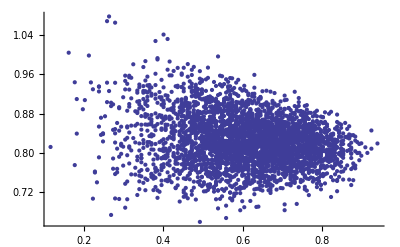

```mathematica
ListPlot[Table[Take[mavenscoremat[[i,28]],-2],{i,3571}]]
```

```mathematica
mavenscore[mavcit_]:=(.94-mavcit[[4]]^2)mavcit[[3]]
```

```mathematica
mavenscore[mavenscoremat[[1,3]]]
```

0.25445

```mathematica
mavcittable=Table[{i,mavenscore[mavenscoremat[[i,1]]]},{i,3571}];
```

```mathematica
mavcit40[citindex_]:=
Take[
Sort[
Table[{i,mavenscore[mavenscoremat[[i,citindex]]],
mavenscoremat[[i,citindex,3]],
mavenscoremat[[i,citindex,4]]},{i,3571}
],
#2[[2]]<#1[[2]]&
],40
];
```

```mathematica
mavcit80[citindex_]:=
Take[
Sort[
Table[{i,mavenscore[mavenscoremat[[i,citindex]]],
mavenscoremat[[i,citindex,3]],
mavenscoremat[[i,citindex,4]]},{i,3571}
],
#2[[2]]<#1[[2]]&
],80
];
```

```mathematica
top40=Table[mavcit40[i],{i,10}];//Timing
```

{0.74466,Null}

```mathematica
top80=Table[mavcit80[i],{i,2000}];//Timing
```

{149.555,Null}

```mathematica
top80>>top80;
```

```mathematica
Dimensions[top80]
```

{2000,80,4}

Find out how many are total flubs and will be evaluated by a mean field method.

```mathematica
a=0;
Do[If[top80[[i,1,2]]≤0, {Print[i],a++}],{i,2000}]
a
```

67

```mathematica
top40>>top40;
```

```mathematica
top80>>top80;
```

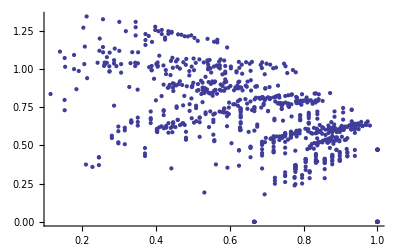

```mathematica
ListPlot[Flatten[Table[Take[top40[[j,i]],-2],{j,20},{i,40}],1]]
```

A couple of estimates of how good the prediction is, using the 80th member of top80 for pessimism.  Taking the Sqrt[] of the square gives a noticeably different result, because the distribution must be quite skewed.

```mathematica
Mean[Flatten[Table[Take[top80[[j,i]],-2]^2,{j,2000},{i,80,80}],1]]
```

{0.45692,0.574882}

```mathematica
Sqrt[.574]
```

0.757628

```mathematica
Mean[Flatten[Table[Take[top80[[j,i]],-2],{j,2000},{i,80,80}],1]]
```

{0.648874,0.712601}

```mathematica
mavenrankings=Table[{i,0},{i,3571}];
Do[mavenrankings[[top80[[i,j,1]],2]]+=top80[[i,j,2]],{i,2000},{j,80}]
```

```mathematica
mavenrankingsint=Table[{i,0},{i,3571}];
Do[mavenrankingsint[[top80[[i,j,1]],2]]+=1,{i,2000},{j,80}]
```

```mathematica
smr2=Sort[mavenrankingsint,#2[[2]]<#1[[2]]&];
```

```mathematica
smr=Sort[mavenrankings,#2[[2]]<#1[[2]]&];
```

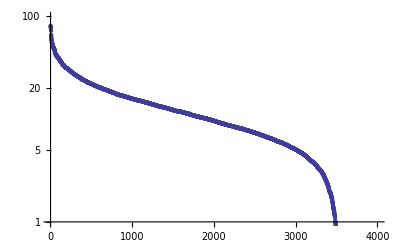

```mathematica
ListLogPlot[Table[{i,smr[[i,2]]},{i,Length[smr]}],PlotRange->{{1,4000},{1,100}}]
```

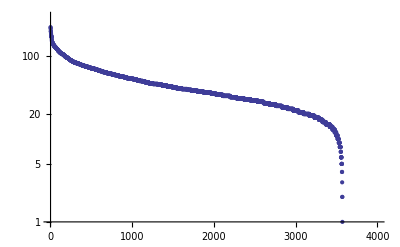

```mathematica
ListLogPlot[Table[{i,smr2[[i,2]]},{i,Length[smr]}],PlotRange->{{1,4000},{1,300}}]
```

```mathematica
membership[mavno_]:={
counter=0;
Do[
{
cml=Table[top80[[i,j,1]],{j,80}];
If[MemberQ[cml,mavno]==True, counter++];
},{i,2000}
];
counter
}[[1]]
```

```mathematica
numbernotincluded[mavcommunitysize_,topxsize_]:=
{
mavcomm=Table[smr[[i,1]],{i,mavcommunitysize}];
misscounter=0;
Do[
{
topvector=Table[top80[[i,j,1]],{j,1,topxsize}];If[Intersection[topvector,mavcomm]=={},misscounter+=1]
},{i,2000}];
misscounter
}[[1]]
```

```mathematica
numberincluded[mavcommunitysize_,topxsize_]:=
{
mavcomm=Table[smr[[i,1]],{i,mavcommunitysize}];
inclcounter=Table[0,{2000}];
Do[
{
topvector=Table[top80[[i,j,1]],{j,1,topxsize}];inclcounter[[i]]=Length[Intersection[topvector,mavcomm]];
},{i,2000}];
}
```

```mathematica
thirdprojector[mavcommunitysize_,topxsize_]:=
{
mavcomm=Table[smr[[i,1]],{i,mavcommunitysize}];
thirdposition=Table[0,{2000}];
Do[
{
topvector=Table[top80[[i,j,1]],{j,1,topxsize}];
j=1;
p=0;
While[j≤topxsize && p<3,If[MemberQ[mavcomm,topvector[[j]]]==True, p++];j++];
thirdposition[[i]]=j;
},{i,2000}];
}
```

```mathematica
seventhprojector[mavcommunitysize_,topxsize_]:=
{
mavcomm=Table[smr[[i,1]],{i,mavcommunitysize}];
seventhposition=Table[0,{2000}];
Do[
{
topvector=Table[top80[[i,j,1]],{j,1,topxsize}];
j=1;
p=0;
While[j≤topxsize && p<7,If[MemberQ[mavcomm,topvector[[j]]]==True, p++];j++];
seventhposition[[i]]=j;
},{i,2000}];
}
```

```mathematica
thirdprojector[600,80]
```

{Null}

```mathematica
Take[top80[[101]],10]
```

{{3108,0.17225,0.586207,0.803842},{529,0.159635,0.789272,0.85892},{393,0.157753,0.505747,0.792515},{1957,0.145661,0.785441,0.868648},{2653,0.145053,0.708812,0.85753},{1713,0.137722,0.551724,0.83089},{1342,0.131964,0.574713,0.842842},{3456,0.124957,0.793103,0.884559},{194,0.124242,0.789272,0.884639},{3438,0.124048,0.727969,0.877267}}

```mathematica
Plus@@Table[If[thirdposition[[i]]==81 ||top80[[i,thirdposition[[i]],4]]>.97, .97,top80[[i,thirdposition[[i]],4]]],{i,2000}]
```

1318.57

```mathematica
Plus@@Table[If[seventhposition[[i]]==81 ||top80[[i,seventhposition[[i]],4]]>1.3, 1.3,top80[[i,seventhposition[[i]],4]]],{i,2000}]
```

1469.35

```mathematica
Sqrt[1469./2000]
```

0.85703

```mathematica
seventhprojector[600,80]
```

{Null}

```mathematica
Histogram[seventhposition]
```

-Graphics-

```mathematica
Histogram[thirdposition]
```

-Graphics-

```mathematica
thirdposition
```

{4,5,9,21}

```mathematica
?While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

```mathematica
tv={3,5,4,6}
mc={1,2,3,4,5,6,7}
```

{3,5,4,6}

{1,2,3,4,5,6,7}

```mathematica
Intersection[tv,mc]
```

{3,4,5,6}

```mathematica
?Intersection
```

Intersection[list_1,list_2,…] gives a sorted list of the elements common to all the list_i.

```mathematica
numberincluded[600,80]
```

{Null}

```mathematica
Mean[inclcounter]//N
```

24.2055

```mathematica
Histogram[inclcounter,78]
```

-Graphics-

```mathematica
Sqrt[.85 .575 + .15 1.55]
```

0.849264

```mathematica
numbernotincluded[225,40]
```

274

```mathematica
mat1=Table[numbernotincluded[100i, 10j],{i,8},{j,8}]
```

{{970,724,596,502,454,407,369,337},{708,473,373,314,273,242,215,197},{528,333,246,211,175,150,136,126},{414,252,179,141,120,103,83,68},{331,202,137,102,79,67,51,43},{284,173,113,81,62,52,41,36},{239,135,85,59,42,34,29,24},{208,116,68,48,35,25,19,16}}

So it looks like the choice that puts the flubs down at the 3% level is about 600 x 50.  This is more intensive than the previous 225 x 25, which produced more than 18% flubs.   Even 225 x 40 produced over 13% flubs.  It's not clear how this interacts with the "bad prediction" list, also about 3%, so to first order I'm making them the same size.

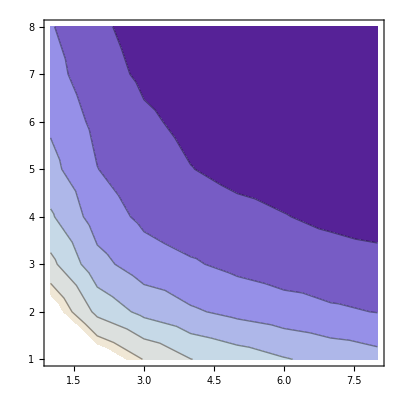

```mathematica
ListContourPlot[mat1]
```

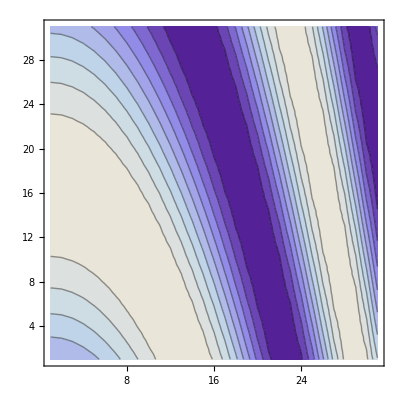

```mathematica
ListContourPlot[Table[Sin[i+j^2],{i,0,3,0.1},{j,0,3,0.1}]]
```

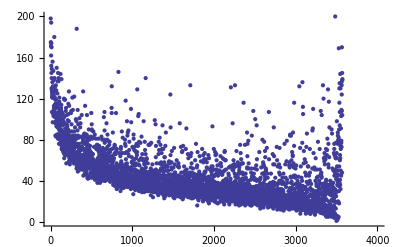

```mathematica
ListPlot[membercount[[2]],PlotRange->{{0,4000},{0,200}}]
```

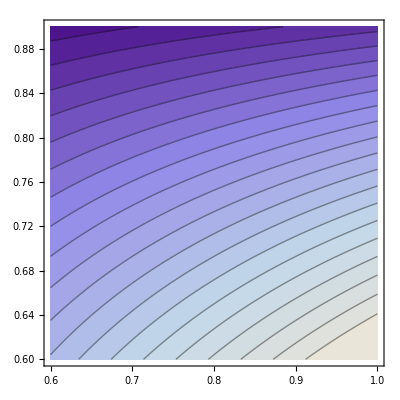

```mathematica
ContourPlot[ x(.94-y^2),{x,0.6,1.0},{y, .6,.9},Contours->20]
```

```mathematica
abm=<<avgbymovie;
rp=<<reviewspers;
```

```mathematica
dbp=<<distbyperson;
```

```mathematica
Dimensions[dbp]
```

{480189,5}

```mathematica
avgbyperson=Table[Sum[dbp[[i,j]] j,{j,1,5}]/Sum[dbp[[i,j]],{j,1,5}],{i,Length[dbp]}]//N;
```

```mathematica
avgbymovie>>avgbyperson;
```

```mathematica
dbp[[3]]
```

{1,2,10,47,38}

```mathematica
abm[[12]]
```

3.41758

```mathematica
rp[[1]]
```

{6,626}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/ProbeStuff"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/ProbeStuff

{probe,probefill,probesorted,probesortsample,pss2}

```mathematica
probe=<<probesorted;
```

```mathematica
Dimensions[probe]
```

{1408395,4}

```mathematica
probe[[125]]
```

{285,250,5,3271}

```mathematica
Take[probe,10]
```

{{825,6,3,3259},{658,6,3,3259},{501,6,3,3259},{9217,7,5,3252},{8393,7,3,3252},{6408,7,5,3252},{285,7,5,3252},{14759,7,3,3252},{1518,8,4,3158},{1428,8,4,3158}}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

```mathematica
rpt=<<reversepersontable;
```

```mathematica
rpt[[6]]
```

1

```mathematica
data=Table[{abm[[probe[[i,1]]]],avgbyperson[[rpt[[probe[[i,2]]]]]],probe[[i,3]]},{i,Length[probe]}];//Timing
```

{4.50727,Null}

```mathematica
data[[33333]]
```

{3.95044,3.1514,4}

```mathematica
MemoryInUse[]
```

100153048

```mathematica
lm=LinearModelFit[data,{1,x,y},{x,y}]
```

FittedModel[-2.96958+0.937082 x+0.884147 y]

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F Statistic | P-Value
x | 1 | 235445. | 235445. | 250821. | 3.22232049663698×10^-50127
y | 1 | 232700. | 232700. | 247896. | 1.38589202758665×10^-49587
Error | 1408392 | 1.32205×10^6 | 0.938698 |  | 
Total | 1408394 | 1.7902×10^6 |  |  |

```mathematica
lm=Fit[data,{1, x, y},{x,y}]
```

-2.96958+0.937082 x+0.884147 y

```mathematica
lm>>meanfieldmodel;
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

```mathematica
%225>>meanfieldmodel;
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F Statistic | P-Value
x | 1 | 4788.58 | 4788.58 | 5139.23 | 1.71507157951313×10^-1029
y | 1 | 4781.52 | 4781.52 | 5131.65 | 4.27008198271174×10^-1028
Error | 28797 | 26832.2 | 0.931771 |  | 
Total | 28799 | 36402.3 |  |  |

After one has identified the 225 mavens of the Knesset, we can start finding the personal mavens for the qualifying subset of citizens.

```mathematica
productionmavensearch[citizenno_,mavenno_,citizennooffset_]:=
{
meanmatrix=Table[0,{i,mavenno},{j,citizenno}];
variancematrix=Table[0,{i,mavenno},{j,citizenno}];
Do[
{
varcompare[getfile[reversepersontable[[mavens[[mavens225[[i]],1]]]]],getfile[j+citizennooffset]];
meanmatrix[[i,j]]=fivemean;
variancematrix[[i,j]]=fivevariance;
Clear[aa];
Clear[fivemean];
Clear[fivevariance];
If[IntegerQ[i/10],Print["i = ",i]]
},
{i,mavenno},{j,citizenno}
];
}
```

```mathematica
productionknessetfind[m_]:=
{mm=Table[thousandmean[[i,m]],{i,225}]/."NaN"->{"NaN","NaN"};
vm=Table[thousandvariance[[i,m]],{i,225}]/."NaN"->1.5;
scores=Table[0,{225}];
norm=Table[0,{225}];
overlaplowercutoff=0.4;
Do[
{
norm[[j]]=Sum[If[mm[[j,k,2]]=="NaN",0.0001,mm[[j,k,2]]],{k,5}];
scores[[j]]={norm[[j]],Sum[If[mm[[j,k,2]]=="NaN", 0, mm[[j,k,2]]] vm[[j,k]],{k,5}]/norm[[j]],j};
},{j,225}
];
scores=DeleteCases[Table[If[scores[[i,1]]/reviewspers[[m+1000,2]]≤overlaplowercutoff&&scores[[i,1]]/mavens[[mavens225[[i]],2]]≤overlaplowercutoff,0,scores[[i]]],{i,225}],0];
(*Histogram[norm/reviewspers[[m,2]]]*)
a1=If[Length[scores]<25, scores, Take[Sort[scores,#2[[2]]>#1[[2]]&],25]];
(*Print[m];*)
Table[{a1[[j,1]]/reviewspers[[m+1000,2]],a1[[j,2]],a1[[j,3]]},{j,Length[a1]}],
Clear[mm,vm,norm,scores];
}[[1]]
```

Here's a little program to see how the maven fitting process is working.  One can look at the interaction of a given maven with the 400 citizens it was vetted against and then throw up the weighted variance performance on a histogram.

```mathematica
Needs["Histograms`"]
```

```mathematica
mavenperuse[m_]:=
{mm=meanmatrix[[m]]/."NaN"->{"NaN","NaN"};
scores=Table[0,{400}];
Do[
{
norm=Sum[If[mm[[j,k,2]]=="NaN",0.01,mm[[j,k,2]]],{k,5}];
scores[[j]]=Sum[If[mm[[j,k,2]]=="NaN", 0, mm[[j,k,2]]] If[variancematrix[[m,j,k]]=="NaN",1.0,variancematrix[[m,j,k]]],{k,5}]/norm;
},{j,400}
];
Histogram[scores]
}
```

Now we need a function that looks at a given citizen across all mavens. One citizen, one movie, one vote.  Create Top 40 by weighting votes for favorites by number of reviews.

```mathematica
citizenperuse[m_]:=
{mm=Table[meanmatrix[[i,m]],{i,3571}]/."NaN"->{"NaN","NaN"};
vm=Table[variancematrix[[i,m]],{i,3571}]/."NaN"->1.5;
scores=Table[0,{3571}];
norm=Table[0,{3571}];
overlaplowercutoff=0.4;
Do[
{
norm[[j]]=Sum[If[mm[[j,k,2]]=="NaN",0.0001,mm[[j,k,2]]],{k,5}];
scores[[j]]={norm[[j]],Sum[If[mm[[j,k,2]]=="NaN", 0, mm[[j,k,2]]] vm[[j,k]],{k,5}]/norm[[j]],j};
},{j,3571}
];
scores=DeleteCases[Table[If[scores[[i,1]]/reviewspers[[m,2]]≤overlaplowercutoff,0,scores[[i]]],{i,3571}],0];
(*Histogram[norm/reviewspers[[m,2]]]*)
a1=If[Length[scores]<40, scores, Take[Sort[scores,#2[[2]]>#1[[2]]&],40]];
Print[m];
Table[{a1[[j,1]]/reviewspers[[m,2]],a1[[j,2]],a1[[j,3]]},{j,Length[a1]}],
Clear[mm,vm,scores,norm];
}[[1]]
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
FileNames[]
```

{avgbymovie,cumreviewplot,distbymovie,distbymoviemp,distbypeoplemp,distbyperson,.DS_Store,fastknesset,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavens,mavensearch,mrplot,peopleids,plotrevbyscorebyperson,popplot,revbyscorebypersonfit,reversepersontable,reviews,reviewsmp,reviewspers,reviewspersmp,seculardrift,titles}

```mathematica
citizenperuse[1]
```

1

{{348/623,0.734376,1026},{286/623,0.734609,96},{344/623,0.735289,1768},{0.59069,0.736746,2594},{276/623,0.741226,2802},{282/623,0.741432,1763},{321/623,0.741592,2983},{428/623,0.741611,1071},{370/623,0.742472,1461},{37/89,0.744164,2609},{381/623,0.745714,1700},{0.58106,0.746465,3314},{47/89,0.747717,917},{291/623,0.748806,111},{325/623,0.749079,3242},{68/89,0.751116,1507},{269/623,0.751285,1613},{360/623,0.751295,1895},{276/623,0.752264,1304},{43/89,0.752406,2313},{405/623,0.752419,3301},{327/623,0.753372,1720},{317/623,0.753514,2433},{410/623,0.753518,628},{382/623,0.7543,2580},{328/623,0.754389,1015},{347/623,0.754467,1566},{0.757625,0.755961,2507},{253/623,0.756068,1805},{338/623,0.756311,1643},{386/623,0.756361,97},{366/623,0.756751,1847},{352/623,0.756773,1039},{405/623,0.756829,2522},{396/623,0.756917,1136},{344/623,0.757418,2272},{0.58748,0.757912,3412},{51/89,0.757984,2308},{49/89,0.758062,752},{311/623,0.758128,869}}

```mathematica
citpts4[[1]]
```

{{348/623,0.734376,1026},{286/623,0.734609,96},{344/623,0.735289,1768},{0.59069,0.736746,2594},{276/623,0.741226,2802},{282/623,0.741432,1763},{321/623,0.741592,2983},{428/623,0.741611,1071},{370/623,0.742472,1461},{37/89,0.744164,2609},{381/623,0.745714,1700},{0.58106,0.746465,3314},{47/89,0.747717,917},{291/623,0.748806,111},{325/623,0.749079,3242},{68/89,0.751116,1507},{269/623,0.751285,1613},{360/623,0.751295,1895},{276/623,0.752264,1304},{43/89,0.752406,2313},{405/623,0.752419,3301},{327/623,0.753372,1720},{317/623,0.753514,2433},{410/623,0.753518,628},{382/623,0.7543,2580},{328/623,0.754389,1015},{347/623,0.754467,1566},{0.757625,0.755961,2507},{253/623,0.756068,1805},{338/623,0.756311,1643},{386/623,0.756361,97},{366/623,0.756751,1847},{352/623,0.756773,1039},{405/623,0.756829,2522},{396/623,0.756917,1136},{344/623,0.757418,2272},{0.58748,0.757912,3412},{51/89,0.757984,2308},{49/89,0.758062,752},{311/623,0.758128,869}}

```mathematica
Mean[Table[Mean[Table[citpts4[[i,j,1]],{j,Length[citpts4[[i]]]}]],{i,400}]]
```

0.570447

```mathematica
Mean[Table[Mean[Table[citpts5[[i,j,1]],{j,Length[citpts5[[i]]]}]],{i,400}]]
```

0.624479

```mathematica
Table[Sum[citpts4[[i,j,2]] reviewspers[[i,2]],{i,400}]/76583.,{j,9}]
```

{0.694127,0.759384,0.769347,0.774883,0.780247,0.78426,0.787226,0.789774,0.792158}

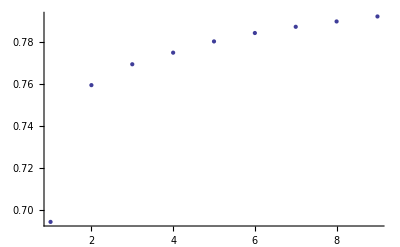

```mathematica
ListPlot[%]
```

```mathematica
Mean[a1]
```

{90.05,0.657485,31619/20}

```mathematica
(*citpts4=Table[citizenperuse[i],{i,400}];*)
```

```mathematica
(*citpts5=Table[citizenperuse[i],{i,400}];*)
```

```mathematica
Tally[Table[Length[citpts5[[i]]],{i,400}]]
```

{{40,394},{13,1},{7,2},{33,1},{25,1},{24,1}}

```mathematica
(*citpts5>>citpts5;*)
```

```mathematica
(*citpts4>>citpts4;*)
```

```mathematica
citpts4=<<citpts4;
```

```mathematica
votetally[depth_]:=
{
votes=Table[{},{3571}];
Do[AppendTo[votes[[citpts4[[i,j,3]]]],i],{i,400},{j,depth}]
}
```

```mathematica
votetally[25]
```

Part::partw: Part 10 of {{0.555578, 0.946372, 177}, {0.7778, 1.1377, 772}, {0.555567, 1.46566, 1058}, « 4 », {0.666689, 0.985669, 3097}, {0.666689, 0.235694, 3307}} does not exist.

Part::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

Part::partw: Part 10 of {{0.555578, 0.946372, 177}, {0.7778, 1.1377, 772}, {0.555567, 1.46566, 1058}, « 4 », {0.666689, 0.985669, 3097}, {0.666689, 0.235694, 3307}} does not exist.

Set::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

Part::partw: Part 11 of {{0.555578, 0.946372, 177}, {0.7778, 1.1377, 772}, {0.555567, 1.46566, 1058}, « 4 », {0.666689, 0.985669, 3097}, {0.666689, 0.235694, 3307}} does not exist.

General::stop: Further output of Part :: "partw" will be suppressed during this calculation.

Part::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

Set::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Set :: "pspec" will be suppressed during this calculation.

{Null}

```mathematica
votes[[1805]]
```

{19,35,105,325}

Weight the maven votes by number of reviews in the cutizens doing the reviewing.  Filter at 1500 so mavens don't vote for themselves.  Use this to pick out the top 225 mavens. Store them.

```mathematica
weightedvotes=Table[{Sum[If[reviewspers[[votes[[i,j]],2]]<1500,reviewspers[[votes[[i,j]],2]],0] ,{j,Length[votes[[i]]]}],i},{i,3571}];
```

```mathematica
maven225data=Take[Sort[weightedvotes,#2[[1]]<#1[[1]]&],225]
```

{{14161,2671},{7550,3471},{7515,1553},{6198,2297},{5946,123},{5431,3304},{5356,2263},{5168,3290},{5131,2592},{4947,2609},{4938,367},{4935,1040},{4829,2539},{4804,637},{4718,3108},{4702,3490},{4699,645},{4524,1660},{4443,3216},{4327,1313},{4291,1415},{4057,1390},{4048,1497},{3967,1064},{3940,3367},{3917,2560},{3912,3442},{3912,1632},{3868,2840},{3856,1703},{3846,2857},{3813,18},{3789,2466},{3789,559},{3754,3063},{3703,400},{3665,1756},{3638,2709},{3598,2433},{3565,3182},{3548,2079},{3543,1471},{3521,1016},{3508,548},{3496,3438},{3490,3315},{3453,1768},{3390,2220},{3388,2974},{3370,1590},{3283,666},{3282,2618},{3273,758},{3232,2790},{3224,1221},{3213,1840},{3202,2491},{3198,1634},{3177,1012},{3175,2041},{3151,1619},{3150,1925},{3147,847},{3137,3509},{3125,3483},{3114,562},{3091,2234},{3087,716},{3079,2906},{3048,2629},{3039,3391},{2996,1219},{2994,280},{2993,1207},{2987,3223},{2973,1727},{2965,2056},{2962,1492},{2954,2946},{2949,3556},{2931,2666},{2910,3195},{2909,3314},{2896,3122},{2888,2791},{2885,665},{2881,2972},{2871,1048},{2858,439},{2816,658},{2813,38},{2793,1269},{2780,3464},{2768,1115},{2765,1053},{2765,131},{2754,1435},{2740,19},{2692,39},{2663,3368},{2662,2313},{2657,3544},{2640,1547},{2624,3281},{2620,2798},{2614,3219},{2614,987},{2587,2653},{2567,1830},{2563,2180},{2563,52},{2555,1018},{2526,2614},{2522,3075},{2517,2331},{2507,756},{2493,1402},{2489,453},{2488,40},{2470,3373},{2470,1584},{2466,1418},{2459,2492},{2449,1990},{2442,2209},{2434,242},{2431,1152},{2416,1647},{2392,1160},{2389,1723},{2374,970},{2364,1651},{2347,2667},{2346,3226},{2327,3569},{2298,1720},{2291,2956},{2273,396},{2269,1084},{2259,780},{2245,2750},{2245,1906},{2243,1203},{2241,233},{2231,2496},{2227,516},{2225,690},{2222,1304},{2219,3080},{2213,1865},{2207,1041},{2201,2447},{2200,784},{2183,2678},{2181,2831},{2175,442},{2170,2052},{2168,3106},{2160,700},{2151,2751},{2140,1141},{2129,115},{2115,2605},{2103,7},{2097,2063},{2088,2275},{2082,672},{2081,3337},{2081,1509},{2062,2996},{2060,3451},{2055,1334},{2054,1589},{2049,497},{2048,547},{2042,3409},{2038,2941},{2037,1216},{2025,1323},{2012,3242},{1994,533},{1987,1955},{1983,2020},{1973,28},{1967,1140},{1962,1643},{1958,2780},{1958,415},{1949,2687},{1945,2801},{1944,181},{1930,109},{1923,3001},{1919,311},{1918,1912},{1913,429},{1910,1124},{1910,70},{1908,210},{1905,350},{1900,3319},{1897,3449},{1897,1490},{1892,750},{1864,2570},{1864,1805},{1863,3160},{1862,1953},{1859,3474},{1859,661},{1855,3016},{1851,1817},{1850,3446},{1846,652},{1841,3035},{1839,1875},{1833,3172},{1829,523},{1827,1103},{1827,1017},{1820,2271},{1818,2198},{1818,64},{1812,1998},{1804,1700}}

```mathematica
mavens225=Table[maven225data[[i,2]],{i,225}]
```

{2671,3471,1553,2297,123,3304,2263,3290,2592,2609,367,1040,2539,637,3108,3490,645,1660,3216,1313,1415,1390,1497,1064,3367,2560,3442,1632,2840,1703,2857,18,2466,559,3063,400,1756,2709,2433,3182,2079,1471,1016,548,3438,3315,1768,2220,2974,1590,666,2618,758,2790,1221,1840,2491,1634,1012,2041,1619,1925,847,3509,3483,562,2234,716,2906,2629,3391,1219,280,1207,3223,1727,2056,1492,2946,3556,2666,3195,3314,3122,2791,665,2972,1048,439,658,38,1269,3464,1115,1053,131,1435,19,39,3368,2313,3544,1547,3281,2798,3219,987,2653,1830,2180,52,1018,2614,3075,2331,756,1402,453,40,3373,1584,1418,2492,1990,2209,242,1152,1647,1160,1723,970,1651,2667,3226,3569,1720,2956,396,1084,780,2750,1906,1203,233,2496,516,690,1304,3080,1865,1041,2447,784,2678,2831,442,2052,3106,700,2751,1141,115,2605,7,2063,2275,672,3337,1509,2996,3451,1334,1589,497,547,3409,2941,1216,1323,3242,533,1955,2020,28,1140,1643,2780,415,2687,2801,181,109,3001,311,1912,429,1124,70,210,350,3319,3449,1490,750,2570,1805,3160,1953,3474,661,3016,1817,3446,652,3035,1875,3172,523,1103,1017,2271,2198,64,1998,1700}

```mathematica
mavens225>>mavens225;
```

```mathematica
votetally[25]
```

Part::partw: Part 10 of {{0.555578, 0.946372, 177}, {0.7778, 1.1377, 772}, {0.555567, 1.46566, 1058}, « 4 », {0.666689, 0.985669, 3097}, {0.666689, 0.235694, 3307}} does not exist.

Part::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

Part::partw: Part 10 of {{0.555578, 0.946372, 177}, {0.7778, 1.1377, 772}, {0.555567, 1.46566, 1058}, « 4 », {0.666689, 0.985669, 3097}, {0.666689, 0.235694, 3307}} does not exist.

Set::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

Part::partw: Part 11 of {{0.555578, 0.946372, 177}, {0.7778, 1.1377, 772}, {0.555567, 1.46566, 1058}, « 4 », {0.666689, 0.985669, 3097}, {0.666689, 0.235694, 3307}} does not exist.

General::stop: Further output of Part :: "partw" will be suppressed during this calculation.

Part::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

Set::pspec: Part specification {{{348/623, 0.734376, 1026}, {286/623, 0.734609, 96}, {344/623, 0.735289, 1768}, {0.59069, 0.736746, 2594}, « 3 », {428/623, 0.741611, 1071}, {370/623, 0.742472, 1461}, {37/89, 0.744164, 2609}, « 30 »}, « 10 »} ⟦ « 1 » ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Set :: "pspec" will be suppressed during this calculation.

{Null}

```mathematica
votes[[1]]
```

{13,233}

```mathematica
citizens=Sort[votes,Length[#2]<Length[#1]&];
```

```mathematica
citizens[[2900]]
```

{}

```mathematica
citlist[n_]:=Tally[Flatten[Table[citizens[[i]],{i,n}],1]]
```

```mathematica
cithits=Sort[citlist[225],#2[[2]]>#1[[2]]&]
```

{{72,1},{122,1},{392,1},{315,1},{71,1},{163,1},{187,1},{338,1},{147,1},{76,1},{323,1},{343,1},{265,1},{225,1},{256,1},{91,1},{57,1},{20,1},{132,1},{100,1},{179,1},{344,1},{155,1},{133,1},{205,1},{371,1},{227,1},{239,1},{235,1},{131,2},{277,2},{183,2},{123,2},{188,2},{280,2},{350,2},{37,2},{304,2},{172,2},{36,2},{87,2},{90,2},{374,2},{11,2},{69,2},{358,2},{372,2},{353,2},{249,2},{400,2},{218,2},{182,2},{50,2},{158,2},{312,2},{319,2},{303,2},{80,2},{153,2},{199,2},{331,2},{266,3},{178,3},{56,3},{381,3},{379,3},{138,3},{310,3},{108,3},{169,3},{27,3},{112,3},{244,3},{351,3},{149,3},{118,3},{61,3},{142,3},{382,3},{201,3},{193,3},{95,3},{21,3},{214,3},{368,3},{333,3},{270,3},{305,3},{352,3},{237,3},{200,3},{367,3},{29,4},{31,4},{386,4},{143,4},{104,4},{384,4},{30,4},{324,4},{181,4},{184,4},{213,4},{18,4},{204,4},{98,4},{24,4},{107,4},{126,4},{136,4},{116,4},{156,4},{84,4},{75,4},{16,4},{349,4},{66,4},{399,4},{233,4},{150,4},{196,4},{369,4},{198,4},{39,4},{321,4},{146,4},{85,4},{284,4},{6,4},{192,4},{202,4},{260,5},{311,5},{174,5},{215,5},{385,5},{365,5},{363,5},{190,5},{373,5},{189,5},{232,5},{209,5},{162,5},{77,5},{102,5},{322,5},{222,5},{297,5},{144,5},{167,5},{388,5},{278,5},{15,5},{5,5},{82,5},{390,5},{55,5},{41,5},{330,5},{255,5},{345,5},{336,5},{286,5},{298,5},{228,5},{393,5},{257,5},{176,5},{78,5},{148,5},{96,5},{366,5},{272,5},{220,5},{119,5},{51,5},{13,5},{283,6},{171,6},{275,6},{59,6},{63,6},{397,6},{151,6},{23,6},{242,6},{89,6},{347,6},{316,6},{292,6},{267,6},{254,6},{130,6},{60,6},{185,6},{212,6},{129,6},{33,6},{10,6},{109,6},{240,6},{268,6},{246,6},{231,6},{160,6},{135,6},{354,6},{264,6},{88,6},{398,6},{362,6},{3,6},{127,6},{210,6},{145,6},{259,6},{211,6},{194,6},{243,6},{152,6},{44,6},{340,6},{289,6},{166,6},{45,7},{12,7},{248,7},{348,7},{7,7},{326,7},{263,7},{271,7},{106,7},{8,7},{302,7},{191,7},{217,7},{219,7},{197,7},{170,7},{4,7},{93,7},{175,7},{86,7},{383,7},{285,7},{377,7},{208,7},{370,7},{139,7},{43,7},{356,7},{81,7},{238,8},{1,8},{206,8},{177,8},{380,8},{274,8},{269,8},{287,8},{332,8},{137,8},{110,8},{294,8},{92,8},{38,8},{308,8},{300,8},{395,8},{337,8},{73,8},{364,8},{223,8},{28,8},{154,8},{26,8},{328,8},{325,8},{120,8},{317,8},{230,8},{125,8},{115,8},{79,9},{97,9},{226,9},{307,9},{101,9},{261,9},{105,9},{357,9},{318,9},{216,9},{236,9},{234,9},{67,9},{168,9},{391,9},{296,9},{313,9},{46,9},{42,9},{346,9},{47,9},{360,10},{94,10},{387,10},{279,10},{361,10},{17,10},{113,10},{83,10},{282,10},{157,10},{376,10},{58,10},{329,10},{114,10},{40,10},{339,10},{334,10},{53,10},{306,10},{342,10},{335,10},{224,10},{70,10},{35,10},{25,10},{19,10},{288,10},{140,10},{128,10},{65,10},{245,11},{203,11},{62,11},{394,11},{141,11},{117,11},{293,11},{165,11},{159,11},{229,11},{180,11},{48,11},{64,11},{276,11},{355,11},{378,11},{341,11},{291,11},{241,11},{54,11},{14,11},{99,12},{327,12},{52,12},{299,12},{262,12},{252,12},{253,12},{9,12},{111,13},{295,13},{281,13},{134,13},{124,13},{68,14},{273,14},{309,14},{161,14},{34,14},{103,15},{207,15},{320,15},{186,15},{121,15},{32,15},{2,15},{49,16},{251,16},{250,16},{359,17},{314,17},{195,17}}

```mathematica
Length[cithits]
```

388

```mathematica
weightsum[n_]:=Sum[reviewspers[[cithits[[i,1]],2]](1-n^cithits[[i,2]]),{i,Length[cithits]}]
```

```mathematica
weightsum[0.44]/76583
```

0.950108

```mathematica
3
```

3

```mathematica
Clear[citlist]
```

```mathematica
citrevs[citlist_]:=Sum[reviewspers[[citlist[[i]],2]],{i,Length[citlist]}]
```

```mathematica
citrevs[citlist[1]]
```

14161

```mathematica
Table[citrevs[citlist[m]]/norm,{m,200}]
```

{15656/76583,1447/5891,26532/76583,697/1781,34655/76583,37031/76583,37794/76583,41291/76583,42478/76583,42993/76583,44052/76583,44461/76583,45728/76583,3631/5891,47690/76583,51629/76583,3986/5891,52071/76583,52502/76583,54414/76583,54872/76583,55372/76583,56300/76583,56933/76583,57896/76583,58464/76583,4732/5891,61978/76583,62035/76583,62080/76583,62325/76583,62340/76583,62646/76583,63048/76583,63755/76583,4921/5891,63983/76583,64060/76583,65031/76583,65361/76583,65419/76583,65983/76583,66084/76583,66914/76583,67030/76583,67233/76583,67245/76583,67245/76583,67638/76583,67764/76583,69038/76583,69038/76583,69038/76583,69421/76583,69421/76583,69436/76583,69469/76583,69477/76583,69477/76583,70998/76583,70998/76583,5466/5891,71441/76583,71755/76583,71839/76583,72131/76583,72586/76583,72862/76583,72996/76583,73459/76583,73459/76583,73459/76583,73469/76583,73526/76583,73526/76583,73585/76583,73585/76583,73585/76583,73640/76583,73640/76583,73640/76583,73652/76583,73652/76583,73857/76583,5703/5891,74183/76583,74183/76583,74183/76583,74290/76583,74290/76583,74290/76583,74850/76583,74850/76583,74850/76583,75040/76583,75040/76583,75118/76583,75118/76583,75118/76583,75118/76583,75172/76583,75172/76583,75172/76583,75262/76583,75262/76583,75349/76583,75349/76583,75349/76583,75349/76583,75349/76583,75360/76583,75360/76583,75360/76583,75360/76583,75360/76583,75404/76583,75404/76583,75404/76583,75404/76583,75404/76583,75404/76583,75404/76583,75437/76583,75437/76583,75483/76583,75502/76583,75502/76583,75502/76583,75502/76583,75547/76583,75547/76583,75593/76583,75593/76583,75601/76583,75601/76583,75601/76583,5820/5891,5820/5891,5820/5891,5820/5891,5820/5891,5820/5891,5820/5891,5825/5891,5825/5891,5825/5891,5825/5891,75774/76583,75774/76583,75774/76583,75774/76583,75774/76583,76150/76583,76150/76583,76150/76583,76150/76583,76150/76583,76150/76583,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559,556/559}

```mathematica
%322[[110]]//N
```

0.983887

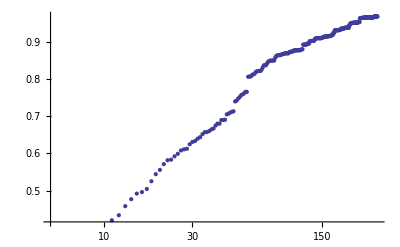

```mathematica
ListLogLinearPlot[%309]
```

```mathematica
Clear[citrevs]
```

```mathematica
norm=Sum[reviewspers[[i,2]],{i,400}]
```

76583

```mathematica
Table[citrevs[n]/norm,{n,4}]
```

Part::pspec: Part specification {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, « 327 »}[1] is neither an integer nor a list of integers.

Part::pspec: Part specification {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, « 327 »}[2] is neither an integer nor a list of integers.

Part::pspec: Part specification {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, « 327 »}[3] is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

$Aborted[]

```mathematica
Table[Length[Union[Flatten[Table[citizens[[i]],{i,m}],1]]],{m,180}]
```

{40,63,76,87,102,116,125,136,144,150,155,161,166,170,174,184,188,193,199,204,208,212,217,221,225,229,232,236,238,239,241,244,245,250,254,259,262,264,270,276,279,284,284,284,288,289,291,291,293,295,297,298,299,301,302,305,307,308,310,311,311,312,312,316,318,319,322,323,326,326,328,329,332,332,333,333,334,335,336,337,338,339,340,340,341,343,343,346,348,349,350,350,351,351,351,352,353,354,354,354,355,356,358,358,359,359,360,362,363,364,365,365,365,365,366,368,368,368,368,369,369,369,371,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,374,375,376,376,376,376,376,376,376,376,377,377,377,377,377,377,377,377,377,377,377,377,378,379,380,380,380,381,382,383}

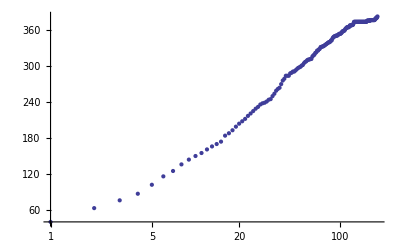

```mathematica
ListLogLinearPlot[%225]
```

```mathematica
Length[Union[Table[citizens[[i]],{i,1}]]]
```

1

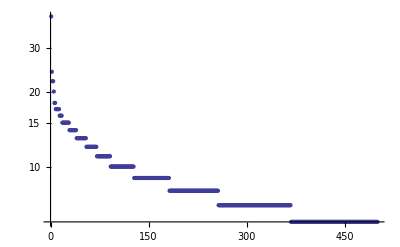

```mathematica
ListLogPlot[Take[Sort[votes,#2<#1&],500]]
```

```mathematica
Mean[citpts3[[1]]]
granddeviation=Sum[Mean[citpts3[[i]]][[2]] reviewspers[[i,2]],{i,400}]/Sum[reviewspers[[i,2]],{i,400}]
granddeviation=Sum[Mean[citpts3[[i]]][[2]] Mean[citpts3[[i]]][[1]],{i,400}]/Sum[Mean[citpts3[[i]]][[1]],{i,400}]
```

```mathematica
Mean[citpts4[[1]]]
granddeviation=Sum[Mean[citpts4[[i]]][[2]] reviewspers[[i,2]],{i,400}]/Sum[reviewspers[[i,2]],{i,400}]
granddeviation=Sum[Mean[citpts4[[i]]][[2]] Mean[citpts4[[i]]][[1]],{i,400}]/Sum[Mean[citpts4[[i]]][[1]],{i,400}]
```

{0.539148,0.738817}

0.77014

0.633774

```mathematica
Mean[citpts5[[1]]]
granddeviation=Sum[Mean[citpts5[[i]]][[2]] reviewspers[[i,2]],{i,400}]/Sum[reviewspers[[i,2]],{i,400}]
granddeviation=Sum[Mean[citpts5[[i]]][[2]] Mean[citpts5[[i]]][[1]],{i,400}]/Sum[Mean[citpts5[[i]]][[1]],{i,400}]
```

{0.596027,0.753068,73841/40}

0.816057

0.710866

```mathematica
MemoryInUse[]
```

1051645360

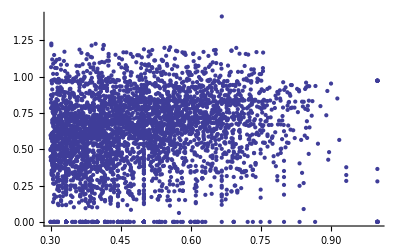

```mathematica
ListPlot[Flatten[citpts2,1]]
```

```mathematica
Histogram[Flatten[bestoverlaps,1]]
```

Histogram::realvec: The first argument to Histogram is expected to be a vector of real values.

Histogram[{Null,Null,Null,Null}]

```mathematica
citizenperuse[111]
```

{0.733137,256.303}

```mathematica
citizenperuse[1]
```

{0.736193,273.902}

Check out how 400 citizens do in terms of their number of movies reviewed and variance (citpts = "citizen points")

```mathematica
citpts>>citpts;
```

```mathematica
citpts15>>citpts15;
```

```mathematica
citpts=<<citpts;
```

```mathematica
ListPlot[citpts]
```

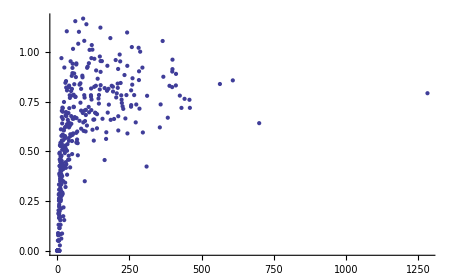

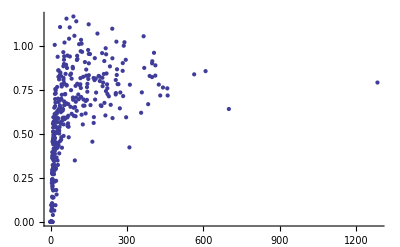

```mathematica
ListPlot[citpts15]
```

Check to see if htere is a systemic connection between degree of overlap and variance.  (if people see all the same movies, are they more likely to agree?)  It doesn't look very compelling at all.  This is probably good news, as I don't then have to account for it.

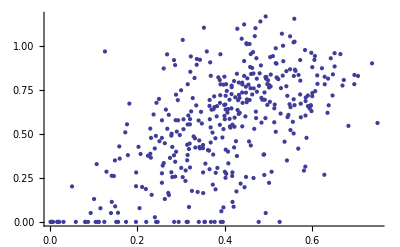

```mathematica
ListPlot[Table[{citpts[[i,1]]/reviewspers[[i,2]],citpts[[i,2]]},{i,Length[citpts]}]]
```

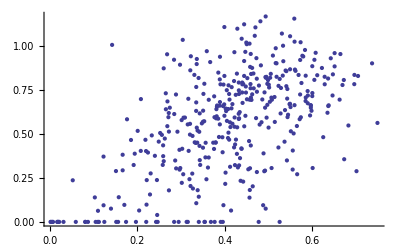

```mathematica
ListPlot[Table[{citpts15[[i,1]]/reviewspers[[i,2]],citpts15[[i,2]]},{i,Length[citpts15]}]]
```

Calculate the overlap/variance scatter, but filter for larger numbers of reviews so as to filter out the lucky ones with zero variance.  It doesn't look too radically different.

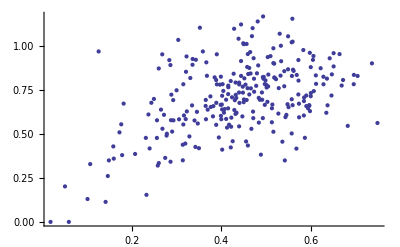

```mathematica
ListPlot[overlapvartable]
```

```mathematica
Sum[citpts[[i,1]]citpts[[i,2]],{i,Length[citpts]}]/Sum[citpts[[i,1]],{i,Length[citpts]}]
```

0.765627

```mathematica
Sum[citpts15[[i,1]]citpts15[[i,2]],{i,Length[citpts15]}]/Sum[citpts15[[i,1]],{i,Length[citpts15]}]
```

0.766093

Is this good news?  I hope so!  It might be a proxy for how well my algorithm will do, accounting for proper weighting.

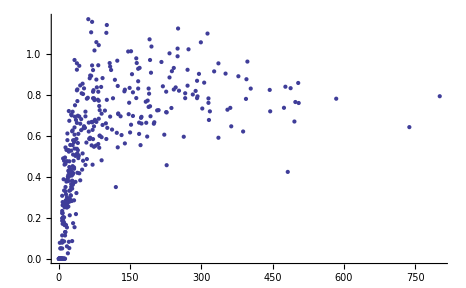

```mathematica
ListPlot[Table[citizenperuse[m],{m,400}]]
```

```mathematica
mavenmatrix=<<mavenmatrix;
```

```mathematica
Dimensions[mavenmatrix]
```

{3571}

```mathematica
Dimensions[Flatten[mavenmatrix]]
```

{20750502}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder

```mathematica
Timing[varcompare[getfile[1111],getfile[1]]]
```

{0.056638,{Null}}

```mathematica
mavens[[10]]
```

{6206,1533}

```mathematica
reversepersontable[[6206]]
```

1111

```mathematica
Timing[varcompare[getfile[reversepersontable[[mavens[[10,1]]]]],getfile[1]]]
```

{0.052606,{Null}}

```mathematica
MemoryInUse[]
```

352661448

### Evaluating

Build a function to see if a particular maven out of the 225 has seen a particular movie and what the score was

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder

```mathematica
getfile[personnumber_]:=
{
aa=Get[peoplefilenames[[personnumber]]];
(*Print["Person number ", personnumber, " corresponds to ", peoplefilenames[[personnumber]], " and has ", Length[aa], " entries"];*)
aa
}[[1]]
```

```mathematica
mavens[[mavens225[[1]],1]]
```

1977824

Make a "quick matrix" of the 225 mavens, each entry 17770 elements long to allow for fast movie comparison, both for generating results and for fast compariosns to generate the Knesset for each citizen.

```mathematica
mavenmoviematrix225=Table[0,{i,225},{j,17770}];
Do[
{mavenscores=getfile[reversepersontable[[mavens[[mavens225[[i]],1]]]]];
Do[
mavenmoviematrix225[[i,mavenscores[[p,1]]]]=mavenscores[[p,2]],{p,Length[mavenscores]}
];
},{i,225}
]
```

```mathematica
piecewisepredictor[citizenthousandno_,movieno_,knessetlistno_]:=
{mavno225=thousandknesset[[citizenthousandno,knessetlistno,3]]; (*Pick out the maven225 in question from the 1000 x 25 citizen-knesset table*)
pppd=mavenmoviematrix225[[mavno225, movieno]];(*Find out what that maven says about the particular movie from the 225 x 17770 mmm*)
(*Print[mavno225];*)
(*Print[pppd];*)
tm=If[pppd==0,0,thousandmean[[mavno225,citizenthousandno,pppd]]];
(*Print[tm];*)
sldkfj=If[Length[tm]==2,tm[[1]],tm](*Apply the offset for the particular citizen*)
}[[1]]
```

```mathematica
piecewisepredictor2[citizenthousandno_,movieno_,knessetlistno_]:=
{mavno225=knetable[[citizenthousandno, knessetlistno,2]]; (*Pick out the maven225 in question from the citizen-knesset table*)
pppd=mavenmoviematrix225[[mavno225, movieno]];(*Find out what that maven says about the particular movie from the 225 x 17770 mmm*)
(*Print[mavno225];*)
(*Print[pppd];*)
tm=If[pppd==0,0,knetable[[citizenthousandno, knessetlistno,5,pppd]]];
(*Print[tm];*)
sldkfj=If[Length[tm]==2,tm[[1]],tm](*Apply the offset for the particular citizen*)
}[[1]]
```

```mathematica
piecewisepredictor3[citizenno_,movieno_,knessetlistno_]:=
{mavno225=knetable[[citizenno, knessetlistno,2]]; (*Pick out the maven225 in question from the citizen-knesset table*)
pppd=mavenmoviematrix225[[mavno225, movieno]];(*Find out what that maven says about the particular movie from the 225 x 17770 mmm*)
(*Print[mavno225];*)
(*Print[pppd];*)
tm=If[pppd==0,0,knetable[[citizenno, knessetlistno,5,pppd]]];
(*Print[tm];*)
sldkfj=If[Length[tm]==2,tm[[1]],tm](*Apply the offset for the particular citizen*)
}[[1]]
```

```mathematica
piecewisepredictor[5,12,1]
```

4.66667

```mathematica
thousandmean[[114,5]]
```

{NaN,{4.25,4},{3.8,10},{5.,7},{4.66667,9}}

```mathematica
Take[mavenmoviematrix225[[114]],20]
```

{0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,4,0,0}

```mathematica
Table[piecewisepredictor[1,i,1],{i,1,20}]
```

{0,0,0,0,4.25,0,0,2.66667,0,0,0,0,0,0,0,3.5,0,0,0,0}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

{avgdist,avgdistpers,avgvector,avgvectorpers,citpts,citpts15,citpts4,citpts5,cumreviewplot,.DS_Store,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavens,mavens225,meanmatrix,mrplot,personalmavs1,personalmavs10,personalmavs15,personalmavs5,personalmavslt5,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift,thousandknesset,thousandmean,thousandvariance,variancematrix}

## Get Fast

How fast can two long vectors be convolved?  Here's two 17k vectors taking about a millisecond:

```mathematica
Timing[mavenmoviematrix225[[5]].mavenmoviematrix225[[32]];]
```

{0.001015,Null}

```mathematica
fastvarcompare[mavenfile1_,file2_]:=
{
(*Print["The first file has ", Length[DeleteCases[mavenfile1,0]] ," entries and second file has ", Length[file2], " entries."];*)
(*movies1=Table[file1[[i,1]],{i,Length[file1]}];
movies2=Table[file2[[i,1]],{i,Length[file2]}];*)
mavencommonscorevector=Table[If[mavenfile1[[file2[[i,1]]]]==0,{0,0},{file2[[i,2]],mavenfile1[[file2[[i,1]]]]}],{i,Length[file2]}];
mavencommonscorevector=DeleteCases[mavencommonscorevector,{0,0}];
stepvariance2go[mavencommonscorevector];
(*Print["There are ", Length[mavencommonscorevector], " movies in the citizen file"];*)
(*overlap=Length[commons]/Min[Length[movies1],Length[movies2]];*)
(*stepvariance2[movies1,movies2,mavenfile1,file2,commons]*)
}
```

```mathematica
cfvc=
Compile[
{{mavenfile1,_Integer,1},{file2,_Integer,2}},
mavencommonscorevector=
Table[
If[
mavenfile1[[file2[[i,1]]]]==0,{0,0},{file2[[i,2]],mavenfile1[[file2[[i,1]]]]}
],{i,Length[file2]}
];
mavencommonscorevector=DeleteCases[mavencommonscorevector,{0,0}];
stepvariance2go[mavencommonscorevector];
(*Print["There are ", Length[mavencommonscorevector], " movies in common."];*)
]
```

```mathematica
stepvariance2go[pairs_]:=
{
fivevector=Table[{},{5}];
Do[AppendTo[fivevector[[pairs[[i,1]]]],pairs[[i]]],{i,Length[pairs]}];
fivemean=Table[0,{5}];
Do[fivemean[[i]]=If[fivevector[[i]]≠{},{Sum[fivevector[[i,j,2]],{j,Length[fivevector[[i]]]}]/Length[fivevector[[i]]]//N,Length[fivevector[[i]]]},{"NaN","NaN"}],{i,5}];
fivevariance=Table[0,{5}];
Do[fivevariance[[i]]=If[Length[fivevector[[i]]]≥2,Sqrt[ Sum[(fivevector[[i,j,2]]-fivemean[[i,1]])^2,{j,Length[fivevector[[i]]]}]/(Length[fivevector[[i]]]-1)],1.5],{i,5}]
}
```

```mathematica
MemoryInUse[]
```

649572704

```mathematica
(*Specify global constants*)
mavenno=225;
overlaplowercutoff=0.4;
epsilon=.0001; (*To prevent divide by zero*)
defaultvariance=1.5;
Timing[
Do[
{SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/TestFolder"];

(*definitions of objects and constants*)
citmavmean=Table[{},{mavenno}];
citmavvariance=Table[0,{mavenno}];
scores=Table[0,{mavenno}];
norm=Table[0,{mavenno}];

(*Get a citizen review file on hot standby*)
a=getfile[j];

(*Compute and store the tables of multiplicities, means, and variances for each of the 225 maven/citizen pairs*)
Do[{cfvc[mavenmoviematrix225[[i]],a];
citmavmean[[i]]=fivemean;
citmavvariance[[i]]=fivevariance;
},{i,1,mavenno}];

(*Grind the stats to rank the mavens and find the knesset for each citizen*)
Do[
{
norm[[m]]=Sum[If[citmavmean[[m,n,2]]=="NaN",epsilon,citmavmean[[m,n,2]]],{n,5}];
scores[[m]]={norm[[m]],Sum[If[citmavmean[[m,n,2]]=="NaN", 0, citmavmean[[m,n,2]]] citmavvariance[[m,n]],{n,5}]/norm[[m]],m};
},{m,mavenno}
];

(*Check to see if the overlap is sufficient to include the score, then rank them*)scores=DeleteCases[Table[If[scores[[i,1]]/reviewspers[[j,2]]≤overlaplowercutoff&&scores[[i,1]]/mavens[[mavens225[[i]],2]]≤overlaplowercutoff,0,scores[[i]]],{i,225}],0];

a1=If[Length[scores]<25, Sort[scores,#2[[2]]>#1[[2]]&], Take[Sort[scores,#2[[2]]>#1[[2]]&],25]];

(*Now put it away*)SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];

a2=Table[{j,a1[[i,3]],a1[[i,1]]/reviewspers[[j,2]],a1[[i,2]],citmavmean[[a1[[i,3]]]]},{i,Length[a1]}];
a2>>>fastknesset;
Clear[a1,a2,scores,citmavmean,citmavvariance,norm,a,aa,fivemean,fivevariance,mavencommonscorevector];
If[IntegerQ[j/100]==True,Print[j]];

},{j,1,20}
]
]
```

{8.66788,Null}

```mathematica
productionknessetfind[m_]:=
{mm=Table[thousandmean[[i,m]],{i,225}]/."NaN"->{"NaN","NaN"};
vm=Table[thousandvariance[[i,m]],{i,225}]/."NaN"->1.5;
scores=Table[0,{225}];
norm=Table[0,{225}];
overlaplowercutoff=0.4;
Do[
{
norm[[j]]=Sum[If[mm[[j,k,2]]=="NaN",0.0001,mm[[j,k,2]]],{k,5}];
scores[[j]]={norm[[j]],Sum[If[mm[[j,k,2]]=="NaN", 0, mm[[j,k,2]]] vm[[j,k]],{k,5}]/norm[[j]],j};
},{j,225}
];
scores=DeleteCases[Table[If[scores[[i,1]]/reviewspers[[m+1000,2]]≤overlaplowercutoff&&scores[[i,1]]/mavens[[mavens225[[i]],2]]≤overlaplowercutoff,0,scores[[i]]],{i,225}],0];
(*Histogram[norm/reviewspers[[m,2]]]*)
a1=If[Length[scores]<25, scores, Take[Sort[scores,#2[[2]]>#1[[2]]&],25]];
(*Print[m];*)
Table[{a1[[j,1]]/reviewspers[[m+1000,2]],a1[[j,2]],a1[[j,3]]},{j,Length[a1]}],
Clear[mm,vm,norm,scores];
}[[1]]
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

{avgdist,avgdistpers,avgvector,avgvectorpers,citpts,citpts15,citpts4,citpts5,cumreviewplot,.DS_Store,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavenmoviematrix225,mavens,mavens225,meanmatrix,mrplot,personalmavs1,personalmavs10,personalmavs15,personalmavs5,personalmavslt5,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift,thousandknesset,thousandmean,thousandvariance,variancematrix}